```mathematica
Quiet[NotebookEvaluate["/Users/Matt/Documents/Research/MIW_mathematica/MIW_header_file.nb"]];
```

Epsilon divergences for perp integrals with non-zero masses

div A0: 2/((D-4) π)

div A1: 0

div A00: m10/((D-4) π)

div A11: 0

div A001: 0

div A111: 0

div A0000: m10^2/(4 (D-4) π)

div A0011: 0

div A1111: 0

div A00001: 0

div A00111: 0

div A11111: 0

div B0: 0

div B1: 0

div B00: 1/((D-4) π)

div B11: 0

div B001: -1/(2 (D-4) π)

div B111: 0

div B0000: (3 (m10+m20)-p10)/(12 (D-4) π)

div B0011: 1/(3 (D-4) π)

div B1111: 0

div B00001: (-2 m10-4 m20+p10)/(24 (D-4) π)

div B00111: -1/(4 (D-4) π)

div B11111: 0

```mathematica
replSingVarPlus[e_]:=e/.PlusDistribution[a_*HeavisideTheta[1-b_]]:>HeavisideTheta[1-b-beta]a-DiracDelta[1-b-beta]Integrate[a,{b,0,b},Assumptions->0<b<1]/.PlusDistribution[a_*HeavisideTheta[b_]]:>HeavisideTheta[b-beta]a+DiracDelta[b-beta]Integrate[a,{b,1,b},Assumptions->0<b<1]


SetAttributes[multiply,HoldAll];
multiply[a_[u_,w_],b_[w_,v_]]:=Module[{tmp1,tmp2,tmp3},
tmp1=a[u,w]*b[w,v]//Expand;
tmp2=tmp1/.DiracDelta[c_]*DiracDelta[d_]:>DiracDelta[c]*someFunc[d];
tmp3=Integrate[tmp2,{w,0,1},Assumptions->0<w<1&&0<u<1&&0<v<1];
Return[tmp3/.someFunc[c_]:> DiracDelta[c]];
];

multiply[a_[u_,w_],b_[w_,v_],c_[v_,z_]]:=Module[{tmp1,tmp2,s,t},
tmp1[s_,t_]:=multiply[b[w,v],c[v,z]]/.w->s/.z->t;
tmp2:=multiply[a[u,s],tmp1[s,t]]/.t->z;
Return[tmp2];
];

$Assumptions=0<delta1<1&&0<delta2<2&&0<xa<1&&0<xb<1&&0<xi1<1&&0<xi2<1&&0<tau<1&&0<tauPerp<1&&tauPM>0&&muMS>0&&s>0
```

0<δ_1<1∧0<δ_2<2∧0<x_a<1∧0<x_b<1∧0<ξ_1<1∧0<ξ_2<1∧0<τ<1∧0<τ_⊥<1∧τ_(+-)>0∧μ_OverBar[MS]>0∧s>0

```mathematica
PlusDistribution[HeavisideTheta[1-x]/(1-x)]//replSingVarPlus
Integrate[%*x,{x,0,1},Assumptions->0<beta<1]

PlusDistribution[HeavisideTheta[x]/(x)]//replSingVarPlus
Integrate[%x,{x,0,1},Assumptions->0<beta<1]
```

log(1-x) x+β-1+(-x-β+1)/(1-x)

β+β (-log(β))-1

log(x) x-β+(x-β)/x

-β+β log(β)+1

```mathematica
(* kinematics *)

(* tau = q^2/s,        tauPerp=qT^2/s , tauPM=tau+tauPerp*)
(* tauHat = q^2/sHat , tauHatPerp = qT^2/sHat *)

(* we use Exp[NEGY] instead of Exp[-Y] to prevent mathemtica from simplifying Exp[-Y] to 1/Exp[Y] -- see the output of Exp[-Y]/(A+B*Exp[-Y])//Simplify *)
applyDYkinematics[e_]:=e/.Vperp[p1]->Vperp[l1]/.Vperp[p2]->Vperp[l2]/.Vperp[k]->Vperp[l1+l2-Q]/.km->p1m+p2m-Sqrt[s]Sqrt[tauPM]*Exp[Y]/.kp->p1p+p2p-Sqrt[s]Sqrt[tauPM]*Exp[NEGY]/.p1p->-SPD[Vperp[l1],Vperp[l1]]/p1m/.p2m->-SPD[Vperp[l2],Vperp[l2]]/p2p/.p1m->xi1*Sqrt[s]/.p2p->xi2*Sqrt[s]/.SPD[Q,Q]->tau*s/.SPD[Vperp[Q],Vperp[Q]]->-tauPerp*s

(* from arXiv:0910.0467v3 or CSS 1985 DY paper *) 
applyXaXbDefn[e_]:=e/.Cosh[NEGY]->Cosh[Y]/.Sinh[NEGY]->-Sinh[Y]/.Cosh[a_*NEGY]:> Cosh[a*Y]/.Sinh[a_*NEGY]:> -Sinh[a*Y]/.Sech[a_]:>1/(Cosh[a]+ZERO)/.Csch[a_]:>1/(Sinh[a]+ZERO)/.Cosh[Y]->( (xa/Sqrt[tau])+(xb/Sqrt[tau]) )/2/.Cosh[a_*Y]:> ( (xa/Sqrt[tau])^a+(xb/Sqrt[tau])^a )/2/.Sinh[Y]->( (xa/Sqrt[tau])-(xb/Sqrt[tau]) )/2/.Sinh[a_*Y]:> ( (xa/Sqrt[tau])^a-(xb/Sqrt[tau])^a )/2/.Exp[Y]->xa/Sqrt[tau]/.Exp[NEGY]->xb/Sqrt[tau]/.Exp[a_*Y]/;a>0:> (xa/Sqrt[tau])^a/.Exp[a_*NEGY]/;a>0:> (xb/Sqrt[tau])^a/.ZERO->0/.tau+tauPerp->tauPM/.NEGY->-Y

applyTauYDefn[e_]:=e/.xa->Sqrt[tau]Exp[Y]/.xb->Sqrt[tau]Exp[-Y]

applyMyDeltaDefn[e_]:=e/.xa*xb->tau/.tau+tauPerp->tauPM/.xa->Sqrt[tau/(tauPM)]*xi1*(1-delta1)/.xb->Sqrt[tau/(tauPM)]*xi2*(1-delta2)

applyTauPerpToDelta[e_]:=e/.tauPerp->(-SPD[Vperp[p1+p2-k],Vperp[p1+p2-k]])/s/.SPD[Vperp[k],Vperp[k]]->-kp*km//applyDYkinematics//applyXaXbDefn//applyMyDeltaDefn

applyAllToDelta[e_]:=e/.tau->tauPM-tauPerp/.tauPM->(1-delta1)*(1-delta2)*xi1*xi2/.tauPerp->delta1*delta2*xi1*xi2

applyDeltaToPerp[e_]:=e/.delta1*delta2->tauPerp/(xi1*xi2)/. 1/(delta1*delta2)->(xi1*xi2)/tauPerp;

reverseDeltaDefn[e_]:=e/.delta1->(1-xa*Sqrt[tauPM/tau]/xi1)/.delta2->(1-xb*Sqrt[tauPM/tau]/xi2)
```

```mathematica
simplifDeltaMinus1[e_]:=e/.(delta1-1)(delta2-1)->tauPM/(xi1*xi2)/. 1/((delta1-1)(delta2-1))->(xi1*xi2)/tauPM/.(delta1+delta2-1)->-tau/(xi1*xi2)//Simplify;
```

#### Testing Relations

```mathematica
y=Log[ (Sqrt[M^2+qT^2Cosh[eta]^2]+qT*Sinh[eta])/Sqrt[M^2+qT^2]]
D[%,{eta,1}]//FullSimplify
```

log((√(M^2+qT^2 cosh^2(η))+qT sinh(η))/(√(M^2+qT^2)))

(qT cosh(η))/(√(M^2+qT^2 cosh^2(η)))

```mathematica
etaa=InverseFunction[(y/.eta->#1)&]
etaa[yy]
%//ExpToTrig
%//FullSimplify
%/.M^2+qT^2->tauP
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

-cosh^-1(-(ⅇ^-#1 √(-2 ⅇ^(2 #1) M^4+ⅇ^(4 #1) M^4+2 ⅇ^(4 #1) M^2 qT^2+2 ⅇ^(2 #1) qT^4+ⅇ^(4 #1) qT^4+M^4+2 M^2 qT^2+qT^4))/(qT √(4 M^2+4 qT^2)))&

-cosh^-1(-(ⅇ^-yy √(-2 M^4 ⅇ^(2 yy)+M^4 ⅇ^(4 yy)+M^4+2 M^2 qT^2 ⅇ^(4 yy)+2 M^2 qT^2+2 qT^4 ⅇ^(2 yy)+qT^4 ⅇ^(4 yy)+qT^4))/(qT √(4 M^2+4 qT^2)))

-cosh^-1(-1/(qT √(4 M^2+4 qT^2))(cosh(yy)-sinh(yy)) √(-2 M^4 sinh(2 yy)+M^4 sinh(4 yy)-2 M^4 cosh(2 yy)+M^4 cosh(4 yy)+M^4+2 M^2 qT^2 sinh(4 yy)+2 M^2 qT^2 cosh(4 yy)+2 M^2 qT^2+2 qT^4 sinh(2 yy)+qT^4 sinh(4 yy)+2 qT^4 cosh(2 yy)+qT^4 cosh(4 yy)+qT^4))

-sech^-1(-(√2 qT ⅇ^yy √(M^2+qT^2))/(√(ⅇ^(2 yy) (M^2+qT^2) ((M^2+qT^2) cosh(2 yy)-M^2+qT^2))))

-sech^-1(-(√2 qT √tauP ⅇ^yy)/(√(tauP ⅇ^(2 yy) (-M^2+qT^2+tauP cosh(2 yy)))))

```mathematica
ppx=(p1m-p1p)/2
ppy=Sqrt[p1m*p1p]

jac11=D[ppx,{p1m,1}]
jac12=D[ppx,{p1p,1}]
jac21=D[ppy,{p1p,1}]
jac22=D[ppy,{p1m,1}]

jac={{jac11,jac12},{jac21,jac22}}
detJac=Det[%]
```

1/2 (p_1^--p_1^+)

√(p_1^+ p_1^-)

1/2

-1/2

p_1^-/(2 √(p_1^+ p_1^-))

p_1^+/(2 √(p_1^+ p_1^-))

(1/2 | -1/2
p_1^-/(2 √(p_1^+ p_1^-)) | p_1^+/(2 √(p_1^+ p_1^-)))

(√(p_1^+ p_1^-))/(4 p_1^+)+(√(p_1^+ p_1^-))/(4 p_1^-)

```mathematica
detJac/.soln
%//FullSimplify
```

{(√(-((√(2 x^2+2 z^2))/(√2)-x) (1/2 (x-(√(2 x^2+2 z^2))/(√2))-x)))/(2 √2 ((√(2 x^2+2 z^2))/(√2)-x))-(√(-((√(2 x^2+2 z^2))/(√2)-x) (1/2 (x-(√(2 x^2+2 z^2))/(√2))-x)))/(4 √2 (1/2 (x-(√(2 x^2+2 z^2))/(√2))-x))}

{(√(x^2+z^2))/(2 √(z^2))}

```mathematica
soln=Solve[{x==ppx,z==ppy,p1p>0,p1m>0,z>0,x>0},{p1m,p1p}]//Normal
%//Normal
```

{{p_1^-→-2 (1/2 (x-(√(2 x^2+2 z^2))/(√2))-x),p_1^+→(√(2 x^2+2 z^2))/(√2)-x}}

{{p_1^-→-2 (1/2 (x-(√(2 x^2+2 z^2))/(√2))-x),p_1^+→(√(2 x^2+2 z^2))/(√2)-x}}

```mathematica
ssigma=(qperp+qpar+Eq)/2

p1perpTilde=2Sqrt[ssigma(ssigma-qperp)(ssigma-qpar)(ssigma-Eq)]/Eq/.qperp->Sqrt[qp*qm]/.qpar->(qm-qp)/2/.Eq->(qm+qp)/2
p1perpTilde=%//FullSimplify
FullSimplify[Series[%,{qp,0,1}]//Normal,Assumptions->qp>0&&qm>0]

p1parTildeSqr=E1^2-p1perpTilde^2/.E1->(p1m+p1p)/2/.p1p->qp*qm/p1m/.p1m->Q-qm
p1parTilde=Sqrt[p1parTildeSqr]
FullSimplify[Series[%,{qp,0,0}]//Normal,Assumptions->qp>0&&Q>qm>0]

p2perpTilde=qperp*E2/Eq/.qperp->Sqrt[qp*qm]/.E2->Q/2/.Eq->(qm+qp)/2
p2perpTilde=%//FullSimplify
FullSimplify[Series[%,{qp,0,1}]//Normal,Assumptions->qp>0&&qm>0]

p1parTildeSqr=E2^2-p2perpTilde^2/.E2->Q/2
p1parTilde=Sqrt[p1parTildeSqr]
FullSimplify[Series[%,{qp,0,0}]//Normal,Assumptions->qp>0&&Q>qm>0]
```

1/2 (Eq+qpar+qperp)

1/(q^++q^-)2 √2 √((1/2 (q^--q^+)+1/2 (q^++q^-)+√(q^+ q^-)) (1/2 (-q^+-q^-)+1/2 (1/2 (q^--q^+)+1/2 (q^++q^-)+√(q^+ q^-))) (1/2 (q^+-q^-)+1/2 (1/2 (q^--q^+)+1/2 (q^++q^-)+√(q^+ q^-))) (1/2 (1/2 (q^--q^+)+1/2 (q^++q^-)+√(q^+ q^-))-√(q^+ q^-)))

(√(q^+ (q^+-q^-)^2 q^-))/(q^++q^-)

√(q^+ q^-)

1/4 ((q^+ q^-)/(Q-q^-)-q^-+Q)^2-(q^+ (q^+-q^-)^2 q^-)/((q^++q^-)^2)

√(1/4 ((q^+ q^-)/(Q-q^-)-q^-+Q)^2-(q^+ (q^+-q^-)^2 q^-)/((q^++q^-)^2))

1/2 (Q-q^-)

(√(q^+ q^-) Q)/(q^++q^-)

(√(q^+ q^-) Q)/(q^++q^-)

√(q^+/q^-) Q

Q^2/4-(q^+ q^- Q^2)/((q^++q^-)^2)

√(Q^2/4-(q^+ q^- Q^2)/((q^++q^-)^2))

Q/2

```mathematica
(p2m)^(abar)
```

### QCD -- can assert that all perps are small

```mathematica
matElem1Dag=-I*g*SpinorUBar[p1].((2FVD[p1,alpha]-GAD[alpha].GSD[k])/(-2SPD[p1,k])).Phatnb.GAD[tau].Phatnb.SpinorV[p2]
matElem2Dag=I*g*SpinorUBar[p1].Phatnb.GAD[tau].Phatnb.((2FVD[p2,alpha]-GSD[k].GAD[alpha])/(-2SPD[p2,k])).SpinorV[p2]

matElemDag=matElem1Dag+matElem2Dag//DiracSimplify//FCE
```

-ⅈ g ū(p_1).(-(2 p_1^α-γ^α.(γ·k))/(2 k·p_1)).(P̂)_(n̄).γ^τ.(P̂)_(n̄).v(p_2)

ⅈ g ū(p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(-(2 p_2^α-(γ·k).γ^α)/(2 k·p_2)).v(p_2)

(ⅈ g p_1^α φ(p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).φ(p_2))/(k·p_1)-(ⅈ g p_2^α φ(p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).φ(p_2))/(k·p_2)+(ⅈ g φ(p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·k).γ^α.φ(p_2))/(2 k·p_2)-(ⅈ g φ(p_1).γ^α.(γ·k).(P̂)_(n̄).γ^τ.(P̂)_(n̄).φ(p_2))/(2 k·p_1)

```mathematica
matElem1=I*g*SpinorVBar[p2].Phatn.GAD[rho].Phatn.((2FVD[p1,alpha]-GSD[k].GAD[alpha])/(-2SPD[p1,k])).SpinorU[p1]
matElem2=-I*g*SpinorVBar[p2].((2FVD[p2,alpha]-GAD[alpha].GSD[k])/(-2SPD[p2,k])).Phatn.GAD[rho].Phatn.SpinorU[p1]

matElem=matElem1+matElem2//DiracSimplify//FCE
```

ⅈ g v̄(p_2).(P̂)_n.γ^ρ.(P̂)_n.(-(2 p_1^α-(γ·k).γ^α)/(2 k·p_1)).u(p_1)

-ⅈ g v̄(p_2).(-(2 p_2^α-γ^α.(γ·k))/(2 k·p_2)).(P̂)_n.γ^ρ.(P̂)_n.u(p_1)

-(ⅈ g p_1^α φ(p_2).(P̂)_n.γ^ρ.(P̂)_n.φ(p_1))/(k·p_1)+(ⅈ g p_2^α φ(p_2).(P̂)_n.γ^ρ.(P̂)_n.φ(p_1))/(k·p_2)+(ⅈ g φ(p_2).(P̂)_n.γ^ρ.(P̂)_n.(γ·k).γ^α.φ(p_1))/(2 k·p_1)-(ⅈ g φ(p_2).γ^α.(γ·k).(P̂)_n.γ^ρ.(P̂)_n.φ(p_1))/(2 k·p_2)

```mathematica
(matElem/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a).(matElemDag/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a)//DiracSimplify//FCE

%//PhatDef//DiracSimplify//FCE
Tr[%]//FCE

trace=%/.SPD[k,k]->0//lcCompAll
```

-(D g^2 (P̂)_n.γ^ρ.(P̂)_n.(γ·k).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(2 k·p_1)+(D g^2 k^2 (P̂)_n.γ^ρ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(4 (k·p_1)^2)-(g^2 (P̂)_n.γ^ρ.(P̂)_n.(γ·k).γ^α.(γ·p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·k).γ^α.(γ·p_2))/(4 k·p_1 k·p_2)-(g^2 γ^α.(γ·k).(P̂)_n.γ^ρ.(P̂)_n.(γ·p_1).γ^α.(γ·k).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(4 k·p_1 k·p_2)+(g^2 γ^α.(γ·k).(P̂)_n.γ^ρ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·k).γ^α.(γ·p_2))/(4 (k·p_2)^2)-(2 g^2 p_1·p_2 (P̂)_n.γ^ρ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(k·p_1 k·p_2)+(g^2 (P̂)_n.γ^ρ.(P̂)_n.(γ·k).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(k·p_1)+(g^2 (P̂)_n.γ^ρ.(P̂)_n.(γ·k).(γ·p_2).(γ·p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(2 k·p_1 k·p_2)+(g^2 (P̂)_n.γ^ρ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·k).(γ·p_1).(γ·p_2))/(2 k·p_1 k·p_2)+(g^2 (P̂)_n.γ^ρ.(P̂)_n.(γ·p_1).(γ·p_2).(γ·k).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(2 k·p_1 k·p_2)+(g^2 (γ·p_1).(γ·k).(P̂)_n.γ^ρ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(2 k·p_1 k·p_2)-(g^2 k^2 (P̂)_n.γ^ρ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(2 (k·p_1)^2)-(g^2 (γ·p_2).(γ·k).(P̂)_n.γ^ρ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(2 (k·p_2)^2)

-(γ^ρ.(γ·k).(γ·n̄).(γ·p_2) k^τ p_1^+ g^2)/(2 k·p_1 k·p_2)+473+(γ^ρ.(γ·p_1).(γ·n).(γ·p_2) (n̄)^τ k^+ k^- g^2)/(4 k·p_1 k·p_2)
 |  |  |  |

((n̄)^ρ (n̄)^τ k^2 p_1^+ p_2^+ g^2)/(k·p_1 k·p_2)+448+(k^+ (p_1^τ p_2^ρ k^--p_1^ρ p_2^τ k^-+18+k^ρ (n̄)^τ p_1·p_2) g^2)/(k·p_1 k·p_2)
 |  |  |  |

-(n^ρ (n̄)^τ (-k^- p_2^+-k^+ p_2^-+2 (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)) g^2)/(1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)-(n^τ 27^ρ (1) g^2)/(1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)-(D 5 g^2)/1+374+1/1-(n^ρ k^+ 3 g^2)/(2 (1)^2)-(n^ρ k^+ 3 g^2)/(2 (1/2 k^- p_2^++1+1)^2)
 |  |  |  |

```mathematica
temp0=trace/.rho->tau//Contract//FCE
temp=%//applyDYkinematics//Simplify
```

-(D k^- p_1^+ (2 k^- p_2^++2 k_⊥·p_2_⊥) g^2)/(2 (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥) (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥))+217+(2 k^+ k^- p_1^+ p_2^- g^2)/((1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥) (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥))
 |  |  |  |

(2 g^2 s ξ_1 ξ_2 (-(D-2)^2 (ⅇ^Y s √(τ_(+-)) ξ_2+(ℓ_2_⊥)^2) (ℓ_1_⊥)^4-(-2 s ξ_1 ξ_2 ℓ_1_⊥·Q_⊥ (D-2)^2+D^2 s^2 ξ_1^2 ξ_2^2-4 D s^2 ξ_1^2 ξ_2^2+4 s^2 ξ_1^2 ξ_2^2-D^2 ⅇ^Y s^2 √(τ_(+-)) ξ_1 ξ_2^2+12 ⅇ^Y s^2 √(τ_(+-)) ξ_1 ξ_2^2+D^2 (ℓ_2_⊥)^4-4 D (ℓ_2_⊥)^4+4 (ℓ_2_⊥)^4-D^2 ⅇ^NEGY s^2 √(τ_(+-)) ξ_1^2 ξ_2+4 D ⅇ^NEGY s^2 √(τ_(+-)) ξ_1^2 ξ_2-4 ⅇ^NEGY s^2 √(τ_(+-)) ξ_1^2 ξ_2+D^2 ⅇ^(NEGY+Y) s^2 τ_(+-) ξ_1 ξ_2-4 D ⅇ^(NEGY+Y) s^2 τ_(+-) ξ_1 ξ_2+4 ⅇ^(NEGY+Y) s^2 τ_(+-) ξ_1 ξ_2+D^2 ⅇ^NEGY s √(τ_(+-)) ξ_1 (ℓ_2_⊥)^2-4 D ⅇ^NEGY s √(τ_(+-)) ξ_1 (ℓ_2_⊥)^2+4 ⅇ^NEGY s √(τ_(+-)) ξ_1 (ℓ_2_⊥)^2-16 D s ξ_1 ξ_2 (ℓ_2_⊥)^2+64 s ξ_1 ξ_2 (ℓ_2_⊥)^2+D^2 ⅇ^Y s √(τ_(+-)) ξ_2 (ℓ_2_⊥)^2-4 D ⅇ^Y s √(τ_(+-)) ξ_2 (ℓ_2_⊥)^2+4 ⅇ^Y s √(τ_(+-)) ξ_2 (ℓ_2_⊥)^2+2 ℓ_1_⊥·ℓ_2_⊥ (s (ξ_1 (D-2)^2+(D^2-12 D+28) ⅇ^Y √(τ_(+-))) ξ_2+(D^2-12 D+28) (ℓ_2_⊥)^2)-2 D^2 s ξ_1 ξ_2 ℓ_2_⊥·Q_⊥+20 D s ξ_1 ξ_2 ℓ_2_⊥·Q_⊥-56 s ξ_1 ξ_2 ℓ_2_⊥·Q_⊥) (ℓ_1_⊥)^2+s ξ_1 (4 D^2 s^2 ξ_1^2 ξ_2^3-24 D s^2 ξ_1^2 ξ_2^3+32 s^2 ξ_1^2 ξ_2^3+D^2 ⅇ^(2 Y) s^2 τ_(+-) ξ_2^3-4 D ⅇ^(2 Y) s^2 τ_(+-) ξ_2^3+4 ⅇ^(2 Y) s^2 τ_(+-) ξ_2^3-4 D^2 ⅇ^Y s^2 √(τ_(+-)) ξ_1 ξ_2^3+24 D ⅇ^Y s^2 √(τ_(+-)) ξ_1 ξ_2^3-32 ⅇ^Y s^2 √(τ_(+-)) ξ_1 ξ_2^3-4 D^2 ⅇ^NEGY s^2 √(τ_(+-)) ξ_1^2 ξ_2^2+24 D ⅇ^NEGY s^2 √(τ_(+-)) ξ_1^2 ξ_2^2-32 ⅇ^NEGY s^2 √(τ_(+-)) ξ_1^2 ξ_2^2-4 D s^2 τ_⊥ ξ_1 ξ_2^2+16 s^2 τ_⊥ ξ_1 ξ_2^2+2 D^2 ⅇ^(NEGY+Y) s^2 τ_(+-) ξ_1 ξ_2^2-12 D ⅇ^(NEGY+Y) s^2 τ_(+-) ξ_1 ξ_2^2+16 ⅇ^(NEGY+Y) s^2 τ_(+-) ξ_1 ξ_2^2-4 D^2 s ξ_1 ℓ_1_⊥·Q_⊥ ξ_2^2+20 D s ξ_1 ℓ_1_⊥·Q_⊥ ξ_2^2-16 s ξ_1 ℓ_1_⊥·Q_⊥ ξ_2^2+2 D^2 ⅇ^Y s √(τ_(+-)) ℓ_1_⊥·Q_⊥ ξ_2^2-16 D ⅇ^Y s √(τ_(+-)) ℓ_1_⊥·Q_⊥ ξ_2^2+32 ⅇ^Y s √(τ_(+-)) ℓ_1_⊥·Q_⊥ ξ_2^2-D^2 s ξ_1 (ℓ_2_⊥)^2 ξ_2^2+4 D s ξ_1 (ℓ_2_⊥)^2 ξ_2^2-4 s ξ_1 (ℓ_2_⊥)^2 ξ_2^2+D^2 ⅇ^Y s √(τ_(+-)) (ℓ_2_⊥)^2 ξ_2^2-4 D ⅇ^Y s √(τ_(+-)) (ℓ_2_⊥)^2 ξ_2^2+4 ⅇ^Y s √(τ_(+-)) (ℓ_2_⊥)^2 ξ_2^2-4 D^2 s ξ_1 ℓ_2_⊥·Q_⊥ ξ_2^2+20 D s ξ_1 ℓ_2_⊥·Q_⊥ ξ_2^2-16 s ξ_1 ℓ_2_⊥·Q_⊥ ξ_2^2+2 D^2 ⅇ^Y s √(τ_(+-)) ℓ_2_⊥·Q_⊥ ξ_2^2-8 D ⅇ^Y s √(τ_(+-)) ℓ_2_⊥·Q_⊥ ξ_2^2+8 ⅇ^Y s √(τ_(+-)) ℓ_2_⊥·Q_⊥ ξ_2^2+D^2 ⅇ^(2 NEGY) s^2 τ_(+-) ξ_1^2 ξ_2-4 D ⅇ^(2 NEGY) s^2 τ_(+-) ξ_1^2 ξ_2+4 ⅇ^(2 NEGY) s^2 τ_(+-) ξ_1^2 ξ_2+8 (D-2) (ℓ_1_⊥·ℓ_2_⊥)^2 ξ_2+2 D^2 ⅇ^NEGY s √(τ_(+-)) ξ_1 ℓ_1_⊥·Q_⊥ ξ_2-8 D ⅇ^NEGY s √(τ_(+-)) ξ_1 ℓ_1_⊥·Q_⊥ ξ_2+8 ⅇ^NEGY s √(τ_(+-)) ξ_1 ℓ_1_⊥·Q_⊥ ξ_2-D^2 ⅇ^(NEGY+Y) s τ_(+-) (ℓ_2_⊥)^2 ξ_2+4 D ⅇ^(NEGY+Y) s τ_(+-) (ℓ_2_⊥)^2 ξ_2-4 ⅇ^(NEGY+Y) s τ_(+-) (ℓ_2_⊥)^2 ξ_2+D^2 ⅇ^NEGY s √(τ_(+-)) ξ_1 (ℓ_2_⊥)^2 ξ_2-12 ⅇ^NEGY s √(τ_(+-)) ξ_1 (ℓ_2_⊥)^2 ξ_2+2 D^2 ℓ_1_⊥·Q_⊥ (ℓ_2_⊥)^2 ξ_2-20 D ℓ_1_⊥·Q_⊥ (ℓ_2_⊥)^2 ξ_2+56 ℓ_1_⊥·Q_⊥ (ℓ_2_⊥)^2 ξ_2+2 D^2 ⅇ^NEGY s √(τ_(+-)) ξ_1 ℓ_2_⊥·Q_⊥ ξ_2-16 D ⅇ^NEGY s √(τ_(+-)) ξ_1 ℓ_2_⊥·Q_⊥ ξ_2+32 ⅇ^NEGY s √(τ_(+-)) ξ_1 ℓ_2_⊥·Q_⊥ ξ_2+8 D ℓ_1_⊥·Q_⊥ ℓ_2_⊥·Q_⊥ ξ_2-32 ℓ_1_⊥·Q_⊥ ℓ_2_⊥·Q_⊥ ξ_2+2 D^2 (ℓ_2_⊥)^2 ℓ_2_⊥·Q_⊥ ξ_2-8 D (ℓ_2_⊥)^2 ℓ_2_⊥·Q_⊥ ξ_2+8 (ℓ_2_⊥)^2 ℓ_2_⊥·Q_⊥ ξ_2-D^2 ⅇ^NEGY √(τ_(+-)) (ℓ_2_⊥)^4+4 D ⅇ^NEGY √(τ_(+-)) (ℓ_2_⊥)^4-4 ⅇ^NEGY √(τ_(+-)) (ℓ_2_⊥)^4-2 ℓ_1_⊥·ℓ_2_⊥ (4 (D-2) ξ_2 ℓ_1_⊥·Q_⊥+(ξ_2 (D-2)^2+(D^2-12 D+28) ⅇ^NEGY √(τ_(+-))) (ℓ_2_⊥)^2+ξ_2 (s (4 τ_⊥+(D^2-12 D+28) ⅇ^(NEGY+Y) τ_(+-)+(D^2-2 D-4) ⅇ^NEGY √(τ_(+-)) ξ_1+(-3 D^2+12 D-4) ξ_1 ξ_2+(D^2-2 D-4) ⅇ^Y √(τ_(+-)) ξ_2)+4 (D-2) ℓ_2_⊥·Q_⊥)))))/((s ξ_1 ξ_2 (s ξ_1 (ξ_2-ⅇ^NEGY √(τ_(+-)))+2 ℓ_1_⊥·ℓ_2_⊥-2 ℓ_1_⊥·Q_⊥)+(ℓ_1_⊥)^2 (ⅇ^Y s √(τ_(+-)) ξ_2+(ℓ_2_⊥)^2)) (2 s ξ_1 ξ_2 ℓ_1_⊥·ℓ_2_⊥+(ⅇ^NEGY s √(τ_(+-)) ξ_1+(ℓ_1_⊥)^2) (ℓ_2_⊥)^2+s ξ_1 ξ_2 (s (ξ_1-ⅇ^Y √(τ_(+-))) ξ_2-2 ℓ_2_⊥·Q_⊥)))

```mathematica
temp/.Vperp[Q]->x*Vperp[Q]/.Vperp[l1]->x*Vperp[l1]/.Vperp[l2]->x*Vperp[l2]/.tauPerp->x^2*tauPerp;
Series[%,{x,0,0}]//Normal//Simplify

%/.D->4//ExpToTrig//Expand;
%//Simplify
LOqcd=%//applyXaXbDefn//Simplify
```

(2 (D-2) g^2 (4 (D-4) ξ_2^2 ξ_1^2+(D-2) ξ_1^2 ⅇ^(2 NEGY) τ_(+-)-4 (D-4) ξ_2 ξ_1^2 ⅇ^NEGY √(τ_(+-))+2 (D-4) ξ_2 ξ_1 τ_(+-) ⅇ^(NEGY+Y)-4 (D-4) ξ_2^2 ξ_1 √(τ_(+-)) ⅇ^Y+(D-2) ξ_2^2 τ_(+-) ⅇ^(2 Y)))/(ξ_1 ξ_2 (ⅇ^NEGY √(τ_(+-))-ξ_2) (√(τ_(+-)) ⅇ^Y-ξ_1))

(8 g^2 τ_(+-) (ξ_1^2 sinh(2 NEGY)+ξ_1^2 cosh(2 NEGY)+ξ_2^2 sinh(2 Y)+ξ_2^2 cosh(2 Y)))/(ξ_1 ξ_2 (ξ_2-√(τ_(+-)) sinh(NEGY)-√(τ_(+-)) cosh(NEGY)) (ξ_1-√(τ_(+-)) sinh(Y)-√(τ_(+-)) cosh(Y)))

(8 g^2 τ_(+-) (ξ_2^2 x_a^2+ξ_1^2 x_b^2))/(ξ_1 ξ_2 (ξ_1 √τ-√(τ_(+-)) x_a) (ξ_2 √τ-√(τ_(+-)) x_b))

### SCET -- when matching at Q, can assert all perps are small

```mathematica
matElemDagN=-I*g*SpinorUBar[p1].((2FVD[p1,alpha]-GAD[alpha].GSD[k])/(-2SPD[p1,k])-FVD[nb,alpha]/(-SPD[nb,k])).Phatnb.GAD[tau].Phatnb.SpinorV[p2]//DiracSimplify//FCE

matElemDagNbar=I*g*SpinorUBar[p1].Phatnb.GAD[tau].Phatnb.((2FVD[p2,alpha]-GSD[k].GAD[alpha])/(-2SPD[p2,k])-FVD[n,alpha]/(-SPD[n,k])).SpinorV[p2]//DiracSimplify//FCE

matElemDagOver=I*g*SpinorUBar[p1].Phatnb.GAD[tau].Phatnb.(FVD[nb,alpha]/(-SPD[nb,k])-FVD[n,alpha]/(-SPD[n,k])).SpinorV[p2]//DiracSimplify//FCE
```

-(ⅈ g (n̄)^α φ(p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).φ(p_2))/k^-+(ⅈ g p_1^α φ(p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).φ(p_2))/(k·p_1)-(ⅈ g φ(p_1).γ^α.(γ·k).(P̂)_(n̄).γ^τ.(P̂)_(n̄).φ(p_2))/(2 k·p_1)

(ⅈ g n^α φ(p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).φ(p_2))/k^+-(ⅈ g p_2^α φ(p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).φ(p_2))/(k·p_2)+(ⅈ g φ(p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·k).γ^α.φ(p_2))/(2 k·p_2)

(ⅈ g n^α φ(p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).φ(p_2))/k^+-(ⅈ g (n̄)^α φ(p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).φ(p_2))/k^-

```mathematica
matElemN=I*g*SpinorVBar[p2].Phatn.GAD[rho].Phatn.((2FVD[p1,alpha]-GSD[k].GAD[alpha])/(-2SPD[p1,k])-FVD[nb,alpha]/(-SPD[nb,k])).SpinorU[p1]//DiracSimplify//FCE

matElemNbar=-I*g*SpinorVBar[p2].((2FVD[p2,alpha]-GAD[alpha].GSD[k])/(-2SPD[p2,k])-FVD[n,alpha]/(-SPD[n,k])).Phatn.GAD[tau].Phatn.SpinorU[p1]//DiracSimplify//FCE

matElemOver=-I*g*SpinorVBar[p2].(FVD[nb,alpha]/(-SPD[nb,k])-FVD[n,alpha]/(-SPD[n,k])).Phatn.GAD[tau].Phatn.SpinorU[p1]//DiracSimplify//FCE
```

(ⅈ g (n̄)^α φ(p_2).(P̂)_n.γ^ρ.(P̂)_n.φ(p_1))/k^--(ⅈ g p_1^α φ(p_2).(P̂)_n.γ^ρ.(P̂)_n.φ(p_1))/(k·p_1)+(ⅈ g φ(p_2).(P̂)_n.γ^ρ.(P̂)_n.(γ·k).γ^α.φ(p_1))/(2 k·p_1)

-(ⅈ g n^α φ(p_2).(P̂)_n.γ^τ.(P̂)_n.φ(p_1))/k^++(ⅈ g p_2^α φ(p_2).(P̂)_n.γ^τ.(P̂)_n.φ(p_1))/(k·p_2)-(ⅈ g φ(p_2).γ^α.(γ·k).(P̂)_n.γ^τ.(P̂)_n.φ(p_1))/(2 k·p_2)

(ⅈ g (n̄)^α φ(p_2).(P̂)_n.γ^τ.(P̂)_n.φ(p_1))/k^--(ⅈ g n^α φ(p_2).(P̂)_n.γ^τ.(P̂)_n.φ(p_1))/k^+

#### N sector

```mathematica
(matElemN/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a).(matElemDagN/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a)//DiracSimplify//FCE

%//PhatDef//DiracSimplify//FCE
Tr[%]//FCE

%/.SPD[k,k]->0//lcCompAll
traceN=%/.Vperp[p1]->Vperp[l1]/.Vperp[p2]->Vperp[l2]/.p1p->-SPD[Vperp[l1],Vperp[l1]]/p1m/.p2m->-SPD[Vperp[l2],Vperp[l2]]/p2p
```

-(D g^2 (P̂)_n.γ^ρ.(P̂)_n.(γ·k).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(2 k·p_1)+(D g^2 k^2 (P̂)_n.γ^ρ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(4 (k·p_1)^2)-(2 g^2 p_1^- (P̂)_n.γ^ρ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(k^- k·p_1)+(g^2 (P̂)_n.γ^ρ.(P̂)_n.(γ·k).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(k·p_1)+(g^2 (P̂)_n.γ^ρ.(P̂)_n.(γ·k).(γ·n̄).(γ·p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(2 k^- k·p_1)+(g^2 (P̂)_n.γ^ρ.(P̂)_n.(γ·p_1).(γ·n̄).(γ·k).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(2 k^- k·p_1)-(g^2 k^2 (P̂)_n.γ^ρ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(2 (k·p_1)^2)

(D g^2 k^2 p_1^- n^τ γ^ρ.(γ·n̄).(γ·n).(γ·p_2))/(16 (k·p_1)^2)-(D g^2 k^- n^τ γ^ρ.(γ·n̄).(γ·n).(γ·p_2))/(8 k·p_1)-(D g^2 k^2 p_1^- n^ρ γ^τ.(γ·n̄).(γ·n).(γ·p_2))/(16 (k·p_1)^2)+(D g^2 k^- n^ρ γ^τ.(γ·n̄).(γ·n).(γ·p_2))/(8 k·p_1)+(D g^2 k^2 p_1^- n^ρ (n̄)^τ (γ·n).(γ·p_2))/(8 (k·p_1)^2)-(D g^2 k^- n^ρ (n̄)^τ (γ·n).(γ·p_2))/(4 k·p_1)-(D g^2 k^2 p_1^- γ^ρ.γ^τ.(γ·n).(γ·p_2))/(8 (k·p_1)^2)+(D g^2 k^- γ^ρ.γ^τ.(γ·n).(γ·p_2))/(4 k·p_1)-(g^2 (p_1^-)^2 n^τ γ^ρ.(γ·n̄).(γ·n).(γ·p_2))/(2 k^- k·p_1)+(g^2 p_1^- n^τ γ^ρ.(γ·n̄).(γ·n).(γ·p_2))/(2 k·p_1)-(g^2 k^2 p_1^- n^τ γ^ρ.(γ·n̄).(γ·n).(γ·p_2))/(8 (k·p_1)^2)+(g^2 k^- n^τ γ^ρ.(γ·n̄).(γ·n).(γ·p_2))/(4 k·p_1)+(g^2 (p_1^-)^2 n^ρ γ^τ.(γ·n̄).(γ·n).(γ·p_2))/(2 k^- k·p_1)-(g^2 p_1^- n^ρ γ^τ.(γ·n̄).(γ·n).(γ·p_2))/(2 k·p_1)+(g^2 k^2 p_1^- n^ρ γ^τ.(γ·n̄).(γ·n).(γ·p_2))/(8 (k·p_1)^2)-(g^2 k^- n^ρ γ^τ.(γ·n̄).(γ·n).(γ·p_2))/(4 k·p_1)-(g^2 (p_1^-)^2 n^ρ (n̄)^τ (γ·n).(γ·p_2))/(k^- k·p_1)+(g^2 p_1^- n^ρ (n̄)^τ (γ·n).(γ·p_2))/(k·p_1)-(g^2 k^2 p_1^- n^ρ (n̄)^τ (γ·n).(γ·p_2))/(4 (k·p_1)^2)+(g^2 k^- n^ρ (n̄)^τ (γ·n).(γ·p_2))/(2 k·p_1)+(g^2 (p_1^-)^2 γ^ρ.γ^τ.(γ·n).(γ·p_2))/(k^- k·p_1)-(g^2 p_1^- γ^ρ.γ^τ.(γ·n).(γ·p_2))/(k·p_1)+(g^2 k^2 p_1^- γ^ρ.γ^τ.(γ·n).(γ·p_2))/(4 (k·p_1)^2)-(g^2 k^- γ^ρ.γ^τ.(γ·n).(γ·p_2))/(2 k·p_1)

-(4 n^ρ (n̄)^τ p_2^+ (p_1^-)^2 g^2)/(k^- k·p_1)+(4 (n^τ p_2^ρ-n^ρ p_2^τ+g^ρτ p_2^+) (p_1^-)^2 g^2)/(k^- k·p_1)-(D n^ρ (n̄)^τ k^- p_2^+ g^2)/(k·p_1)+(2 n^ρ (n̄)^τ k^- p_2^+ g^2)/(k·p_1)+(D k^- (n^τ p_2^ρ-n^ρ p_2^τ+g^ρτ p_2^+) g^2)/(k·p_1)-(2 k^- (n^τ p_2^ρ-n^ρ p_2^τ+g^ρτ p_2^+) g^2)/(k·p_1)+(4 n^ρ (n̄)^τ p_2^+ p_1^- g^2)/(k·p_1)+(D n^ρ (n̄)^τ k^2 p_2^+ p_1^- g^2)/(2 (k·p_1)^2)-(n^ρ (n̄)^τ k^2 p_2^+ p_1^- g^2)/(k·p_1)^2-(4 (n^τ p_2^ρ-n^ρ p_2^τ+g^ρτ p_2^+) p_1^- g^2)/(k·p_1)-(D k^2 (n^τ p_2^ρ-n^ρ p_2^τ+g^ρτ p_2^+) p_1^- g^2)/(2 (k·p_1)^2)+(k^2 (n^τ p_2^ρ-n^ρ p_2^τ+g^ρτ p_2^+) p_1^- g^2)/(k·p_1)^2-(2 n^τ (p_1^-)^2 (2 p_2^ρ+(n̄)^ρ p_2^+-n^ρ p_2^-) g^2)/(k^- k·p_1)+(2 n^τ p_1^- (2 p_2^ρ+(n̄)^ρ p_2^+-n^ρ p_2^-) g^2)/(k·p_1)+(D n^τ k^2 p_1^- (2 p_2^ρ+(n̄)^ρ p_2^+-n^ρ p_2^-) g^2)/(4 (k·p_1)^2)-(n^τ k^2 p_1^- (2 p_2^ρ+(n̄)^ρ p_2^+-n^ρ p_2^-) g^2)/(2 (k·p_1)^2)-(D n^τ k^- (2 p_2^ρ+(n̄)^ρ p_2^+-n^ρ p_2^-) g^2)/(2 k·p_1)+(n^τ k^- (2 p_2^ρ+(n̄)^ρ p_2^+-n^ρ p_2^-) g^2)/(k·p_1)+(2 n^ρ (p_1^-)^2 (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-) g^2)/(k^- k·p_1)-(2 n^ρ p_1^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-) g^2)/(k·p_1)-(D n^ρ k^2 p_1^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-) g^2)/(4 (k·p_1)^2)+(n^ρ k^2 p_1^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-) g^2)/(2 (k·p_1)^2)+(D n^ρ k^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-) g^2)/(2 k·p_1)-(n^ρ k^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-) g^2)/(k·p_1)

-(4 n^ρ (n̄)^τ p_2^+ (p_1^-)^2 g^2)/(k^- (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥))-(D n^ρ (n̄)^τ k^- p_2^+ g^2)/(1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)+(2 n^ρ (n̄)^τ k^- p_2^+ g^2)/(1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)+(4 n^ρ (n̄)^τ p_2^+ p_1^- g^2)/(1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)-(2 n^τ (p_1^-)^2 ((n̄)^ρ p_2^+-n^ρ p_2^-+2 ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)) g^2)/(k^- (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥))-(D n^τ k^- ((n̄)^ρ p_2^+-n^ρ p_2^-+2 ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)) g^2)/(2 (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥))+(n^τ k^- ((n̄)^ρ p_2^+-n^ρ p_2^-+2 ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)) g^2)/(1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)+(2 n^τ p_1^- ((n̄)^ρ p_2^+-n^ρ p_2^-+2 ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)) g^2)/(1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)+(2 n^ρ (p_1^-)^2 ((n̄)^τ p_2^+-n^τ p_2^-+2 ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)) g^2)/(k^- (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥))+(D n^ρ k^- ((n̄)^τ p_2^+-n^τ p_2^-+2 ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)) g^2)/(2 (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥))-(n^ρ k^- ((n̄)^τ p_2^+-n^τ p_2^-+2 ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)) g^2)/(1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)-(2 n^ρ p_1^- ((n̄)^τ p_2^+-n^τ p_2^-+2 ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)) g^2)/(1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)+(4 (p_1^-)^2 (g^ρτ p_2^++n^τ ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)-n^ρ ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)) g^2)/(k^- (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥))+(D k^- (g^ρτ p_2^++n^τ ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)-n^ρ ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)) g^2)/(1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)-(2 k^- (g^ρτ p_2^++n^τ ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)-n^ρ ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)) g^2)/(1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)-(4 p_1^- (g^ρτ p_2^++n^τ ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)-n^ρ ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)) g^2)/(1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)

-(2 n^τ (p_1^-)^2 ((n̄)^ρ p_2^++2 ((ℓ_2_⊥)^ρ+1/2 (n̄)^ρ p_2^+-(n^ρ (ℓ_2_⊥)^2)/(2 p_2^+))+(n^ρ (ℓ_2_⊥)^2)/p_2^+) g^2)/(k^- (1/2 k^+ p_1^-+k_⊥·ℓ_1_⊥-(k^- (ℓ_1_⊥)^2)/(2 p_1^-)))-(D n^τ k^- ((n̄)^ρ p_2^++2 ((ℓ_2_⊥)^ρ+1/2 (n̄)^ρ p_2^+-(n^ρ (ℓ_2_⊥)^2)/(2 p_2^+))+(n^ρ (ℓ_2_⊥)^2)/p_2^+) g^2)/(2 (1/2 k^+ p_1^-+k_⊥·ℓ_1_⊥-(k^- (ℓ_1_⊥)^2)/(2 p_1^-)))+(n^τ k^- ((n̄)^ρ p_2^++2 ((ℓ_2_⊥)^ρ+1/2 (n̄)^ρ p_2^+-(n^ρ (ℓ_2_⊥)^2)/(2 p_2^+))+(n^ρ (ℓ_2_⊥)^2)/p_2^+) g^2)/(1/2 k^+ p_1^-+k_⊥·ℓ_1_⊥-(k^- (ℓ_1_⊥)^2)/(2 p_1^-))+(2 n^τ p_1^- ((n̄)^ρ p_2^++2 ((ℓ_2_⊥)^ρ+1/2 (n̄)^ρ p_2^+-(n^ρ (ℓ_2_⊥)^2)/(2 p_2^+))+(n^ρ (ℓ_2_⊥)^2)/p_2^+) g^2)/(1/2 k^+ p_1^-+k_⊥·ℓ_1_⊥-(k^- (ℓ_1_⊥)^2)/(2 p_1^-))+(2 n^ρ (p_1^-)^2 ((n̄)^τ p_2^++2 ((ℓ_2_⊥)^τ+1/2 (n̄)^τ p_2^+-(n^τ (ℓ_2_⊥)^2)/(2 p_2^+))+(n^τ (ℓ_2_⊥)^2)/p_2^+) g^2)/(k^- (1/2 k^+ p_1^-+k_⊥·ℓ_1_⊥-(k^- (ℓ_1_⊥)^2)/(2 p_1^-)))+(D n^ρ k^- ((n̄)^τ p_2^++2 ((ℓ_2_⊥)^τ+1/2 (n̄)^τ p_2^+-(n^τ (ℓ_2_⊥)^2)/(2 p_2^+))+(n^τ (ℓ_2_⊥)^2)/p_2^+) g^2)/(2 (1/2 k^+ p_1^-+k_⊥·ℓ_1_⊥-(k^- (ℓ_1_⊥)^2)/(2 p_1^-)))-(n^ρ k^- ((n̄)^τ p_2^++2 ((ℓ_2_⊥)^τ+1/2 (n̄)^τ p_2^+-(n^τ (ℓ_2_⊥)^2)/(2 p_2^+))+(n^τ (ℓ_2_⊥)^2)/p_2^+) g^2)/(1/2 k^+ p_1^-+k_⊥·ℓ_1_⊥-(k^- (ℓ_1_⊥)^2)/(2 p_1^-))-(2 n^ρ p_1^- ((n̄)^τ p_2^++2 ((ℓ_2_⊥)^τ+1/2 (n̄)^τ p_2^+-(n^τ (ℓ_2_⊥)^2)/(2 p_2^+))+(n^τ (ℓ_2_⊥)^2)/p_2^+) g^2)/(1/2 k^+ p_1^-+k_⊥·ℓ_1_⊥-(k^- (ℓ_1_⊥)^2)/(2 p_1^-))+(4 (p_1^-)^2 (g^ρτ p_2^++n^τ ((ℓ_2_⊥)^ρ+1/2 (n̄)^ρ p_2^+-(n^ρ (ℓ_2_⊥)^2)/(2 p_2^+))-n^ρ ((ℓ_2_⊥)^τ+1/2 (n̄)^τ p_2^+-(n^τ (ℓ_2_⊥)^2)/(2 p_2^+))) g^2)/(k^- (1/2 k^+ p_1^-+k_⊥·ℓ_1_⊥-(k^- (ℓ_1_⊥)^2)/(2 p_1^-)))+(D k^- (g^ρτ p_2^++n^τ ((ℓ_2_⊥)^ρ+1/2 (n̄)^ρ p_2^+-(n^ρ (ℓ_2_⊥)^2)/(2 p_2^+))-n^ρ ((ℓ_2_⊥)^τ+1/2 (n̄)^τ p_2^+-(n^τ (ℓ_2_⊥)^2)/(2 p_2^+))) g^2)/(1/2 k^+ p_1^-+k_⊥·ℓ_1_⊥-(k^- (ℓ_1_⊥)^2)/(2 p_1^-))-(2 k^- (g^ρτ p_2^++n^τ ((ℓ_2_⊥)^ρ+1/2 (n̄)^ρ p_2^+-(n^ρ (ℓ_2_⊥)^2)/(2 p_2^+))-n^ρ ((ℓ_2_⊥)^τ+1/2 (n̄)^τ p_2^+-(n^τ (ℓ_2_⊥)^2)/(2 p_2^+))) g^2)/(1/2 k^+ p_1^-+k_⊥·ℓ_1_⊥-(k^- (ℓ_1_⊥)^2)/(2 p_1^-))-(4 p_1^- (g^ρτ p_2^++n^τ ((ℓ_2_⊥)^ρ+1/2 (n̄)^ρ p_2^+-(n^ρ (ℓ_2_⊥)^2)/(2 p_2^+))-n^ρ ((ℓ_2_⊥)^τ+1/2 (n̄)^τ p_2^+-(n^τ (ℓ_2_⊥)^2)/(2 p_2^+))) g^2)/(1/2 k^+ p_1^-+k_⊥·ℓ_1_⊥-(k^- (ℓ_1_⊥)^2)/(2 p_1^-))-(4 n^ρ (n̄)^τ p_2^+ (p_1^-)^2 g^2)/(k^- (1/2 k^+ p_1^-+k_⊥·ℓ_1_⊥-(k^- (ℓ_1_⊥)^2)/(2 p_1^-)))-(D n^ρ (n̄)^τ k^- p_2^+ g^2)/(1/2 k^+ p_1^-+k_⊥·ℓ_1_⊥-(k^- (ℓ_1_⊥)^2)/(2 p_1^-))+(2 n^ρ (n̄)^τ k^- p_2^+ g^2)/(1/2 k^+ p_1^-+k_⊥·ℓ_1_⊥-(k^- (ℓ_1_⊥)^2)/(2 p_1^-))+(4 n^ρ (n̄)^τ p_2^+ p_1^- g^2)/(1/2 k^+ p_1^-+k_⊥·ℓ_1_⊥-(k^- (ℓ_1_⊥)^2)/(2 p_1^-))

```mathematica
temp0N=traceN/.rho->tau//Contract//FCE
tempN=%//applyDYkinematics//Simplify
```

(D^2 g^2 k^- p_2^+)/(-(k^- (ℓ_1_⊥)^2)/(2 p_1^-)+1/2 k^+ p_1^-+k_⊥·ℓ_1_⊥)+(4 D g^2 p_2^+ (p_1^-)^2)/(k^- (-(k^- (ℓ_1_⊥)^2)/(2 p_1^-)+1/2 k^+ p_1^-+k_⊥·ℓ_1_⊥))-(4 D g^2 k^- p_2^+)/(-(k^- (ℓ_1_⊥)^2)/(2 p_1^-)+1/2 k^+ p_1^-+k_⊥·ℓ_1_⊥)-(4 D g^2 p_2^+ p_1^-)/(-(k^- (ℓ_1_⊥)^2)/(2 p_1^-)+1/2 k^+ p_1^-+k_⊥·ℓ_1_⊥)-(8 g^2 p_2^+ (p_1^-)^2)/(k^- (-(k^- (ℓ_1_⊥)^2)/(2 p_1^-)+1/2 k^+ p_1^-+k_⊥·ℓ_1_⊥))+(4 g^2 k^- p_2^+)/(-(k^- (ℓ_1_⊥)^2)/(2 p_1^-)+1/2 k^+ p_1^-+k_⊥·ℓ_1_⊥)+(8 g^2 p_2^+ p_1^-)/(-(k^- (ℓ_1_⊥)^2)/(2 p_1^-)+1/2 k^+ p_1^-+k_⊥·ℓ_1_⊥)

-((2 (D-2) g^2 ξ_1 ξ_2 s (ξ_2^2 s^2 ((D-2) ξ_1^2-2 (D-4) ξ_1 √(τ_(+-)) ⅇ^Y+(D-2) τ_(+-) ⅇ^(2 Y))+2 ξ_2 s (ℓ_2_⊥)^2 ((D-2) √(τ_(+-)) ⅇ^Y-(D-4) ξ_1)+(D-2) (ℓ_2_⊥)^4))/((ξ_2 s (√(τ_(+-)) ⅇ^Y-ξ_1)+(ℓ_2_⊥)^2) (ξ_1 ξ_2 s (ξ_1 s (ξ_2-ⅇ^NEGY √(τ_(+-)))-2 ℓ_1_⊥·Q_⊥+2 ℓ_1_⊥·ℓ_2_⊥)+(ℓ_1_⊥)^2 (ξ_2 s √(τ_(+-)) ⅇ^Y+(ℓ_2_⊥)^2))))

```mathematica
tempN/.Vperp[Q]->x*Vperp[Q]/.Vperp[l1]->x*Vperp[l1]/.Vperp[l2]->x*Vperp[l2]/.tauPerp->x^2*tauPerp;
LOtempN=Series[%,{x,0,0}]//Normal//Simplify

%/.D->4-2*eps//ExpToTrig//Expand;
%//Simplify
LOsectorN=%//applyXaXbDefn//Simplify
```

(2 (D-2) g^2 ξ_2 ((D-2) ξ_1^2-2 (D-4) ξ_1 √(τ_(+-)) ⅇ^Y+(D-2) τ_(+-) ⅇ^(2 Y)))/(ξ_1 (ⅇ^NEGY √(τ_(+-))-ξ_2) (√(τ_(+-)) ⅇ^Y-ξ_1))

(8 g^2 ξ_2 (ϵ-1) (sinh(Y)+cosh(Y)) ((ϵ-1) (τ_(+-)-ξ_1^2) sinh(Y)+(ϵ-1) (ξ_1^2+τ_(+-)) cosh(Y)-2 ξ_1 √(τ_(+-)) ϵ))/(ξ_1 (ξ_2-√(τ_(+-)) sinh(NEGY)-√(τ_(+-)) cosh(NEGY)) (ξ_1-√(τ_(+-)) sinh(Y)-√(τ_(+-)) cosh(Y)))

-(8 g^2 ξ_2 (ϵ-1) x_a (τ_(+-) (ϵ-1) x_a+ξ_1 (ξ_1 (ϵ-1) x_b-2 √(τ_(+-) τ) ϵ)))/(ξ_1 (ξ_1 √τ-√(τ_(+-)) x_a) (√(τ_(+-)) x_b-ξ_2 √τ))

```mathematica
LOsectorN//applyMyDeltaDefn//Simplify
Ndelta=Collect2[%,tau]//simplifDeltaMinus1//Simplify
%*(sHat*delta1)^(-eps)*(delta2)^(-eps)
NdeltaPlus=%/.a_^(-1-eps):>-Inactive[DiracDelta][a]/eps+PlusDistribution[Inactive[HeavisideTheta][a]/a]-eps*PlusDistribution[Inactive[HeavisideTheta][a]Log[a]/a]
Series[%,{eps,0,0}]//Normal//Simplify
```

(8 (δ_1-1) g^2 (ϵ-1) ((δ_2-1) ξ_1 ξ_2 √(τ/(τ_(+-))) (ϵ-1)+√(τ_(+-) τ) (δ_1 (ϵ-1)+ϵ+1)))/(δ_1 δ_2 √(τ_(+-) τ))

(8 g^2 (ϵ-1) (δ_1^2 (ϵ-1)+2 δ_1-2))/(δ_1 δ_2)

(8 g^2 (ϵ-1) δ_2^(-ϵ-1) (δ_1^2 (ϵ-1)+2 δ_1-2) (δ_1 ŝ)^-ϵ)/δ_1

(8 g^2 (ϵ-1) (δ_1^2 (ϵ-1)+2 δ_1-2) (δ_1 ŝ)^-ϵ (-δ[δ_2]/ϵ+(θ[δ_2]/δ_2)_+-ϵ ((log(δ_2) θ[δ_2])/δ_2)_+))/δ_1

(8 g^2 ((2 δ_1^2-2 δ_1+(δ_1^2-2 δ_1+2) log(δ_1 ŝ)+2) δ[δ_2]+(δ_1^2-2 δ_1+2) (θ[δ_2]/δ_2)_+))/δ_1-(8 (δ_1^2-2 δ_1+2) g^2 δ[δ_2])/(δ_1 ϵ)

#### Nbar sector

```mathematica
(matElemNbar/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a).(matElemDagNbar/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a)//DiracSimplify//FCE

%//PhatDef//DiracSimplify//FCE
Tr[%]//FCE

%/.SPD[k,k]->0//lcCompAll
traceNbar=%/.Vperp[p1]->Vperp[l1]/.Vperp[p2]->Vperp[l2]/.p1p->-SPD[Vperp[l1],Vperp[l1]]/p1m/.p2m->-SPD[Vperp[l2],Vperp[l2]]/p2p
```

(g^2 γ^α.(γ·k).(P̂)_n.γ^τ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·k).γ^α.(γ·p_2))/(4 (k·p_2)^2)-(2 g^2 p_2^+ (P̂)_n.γ^τ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(k^+ k·p_2)+(g^2 (P̂)_n.γ^τ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·k).(γ·n).(γ·p_2))/(2 k^+ k·p_2)+(g^2 (γ·n).(γ·k).(P̂)_n.γ^τ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(2 k^+ k·p_2)-(g^2 (γ·p_2).(γ·k).(P̂)_n.γ^τ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(2 (k·p_2)^2)

-(D^2 g^2 k^2 p_1^- (γ·n).(γ·p_2))/(8 (k·p_2)^2)+(D^2 g^2 k^+ p_1^- (γ·k).(γ·p_2))/(4 (k·p_2)^2)+(D g^2 p_2^+ p_1^- (γ·n).(γ·p_2))/(k^+ k·p_2)-(D g^2 p_1^- (γ·n).(γ·p_2))/(2 k·p_2)+(D g^2 k^2 p_1^- (γ·n).(γ·p_2))/(2 (k·p_2)^2)-(D g^2 p_2^+ p_1^- (γ·k).(γ·p_2))/(2 (k·p_2)^2)-(D g^2 k^+ p_1^- (γ·k).(γ·p_2))/(k·p_2)^2-(2 g^2 p_2^+ p_1^- (γ·n).(γ·p_2))/(k^+ k·p_2)+(g^2 p_1^- (γ·n).(γ·p_2))/(k·p_2)-(g^2 k^2 p_1^- (γ·n).(γ·p_2))/(2 (k·p_2)^2)+(g^2 p_2^+ p_1^- (γ·k).(γ·p_2))/(k·p_2)^2+(g^2 k^+ p_1^- (γ·k).(γ·p_2))/(k·p_2)^2

-(D^2 g^2 k^2 p_2^+ p_1^-)/(2 (k·p_2)^2)+(D^2 g^2 k^+ p_1^-)/(k·p_2)+(4 D g^2 (p_2^+)^2 p_1^-)/(k^+ k·p_2)-(4 D g^2 p_2^+ p_1^-)/(k·p_2)+(2 D g^2 k^2 p_2^+ p_1^-)/(k·p_2)^2-(4 D g^2 k^+ p_1^-)/(k·p_2)-(8 g^2 (p_2^+)^2 p_1^-)/(k^+ k·p_2)+(8 g^2 p_2^+ p_1^-)/(k·p_2)-(2 g^2 k^2 p_2^+ p_1^-)/(k·p_2)^2+(4 g^2 k^+ p_1^-)/(k·p_2)

(D^2 g^2 k^+ p_1^-)/(1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)+(4 D g^2 (p_2^+)^2 p_1^-)/(k^+ (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥))-(4 D g^2 k^+ p_1^-)/(1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)-(4 D g^2 p_2^+ p_1^-)/(1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)-(8 g^2 (p_2^+)^2 p_1^-)/(k^+ (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥))+(4 g^2 k^+ p_1^-)/(1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)+(8 g^2 p_2^+ p_1^-)/(1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)

(D^2 g^2 k^+ p_1^-)/(-(k^+ (ℓ_2_⊥)^2)/(2 p_2^+)+1/2 k^- p_2^++k_⊥·ℓ_2_⊥)+(4 D g^2 (p_2^+)^2 p_1^-)/(k^+ (-(k^+ (ℓ_2_⊥)^2)/(2 p_2^+)+1/2 k^- p_2^++k_⊥·ℓ_2_⊥))-(4 D g^2 k^+ p_1^-)/(-(k^+ (ℓ_2_⊥)^2)/(2 p_2^+)+1/2 k^- p_2^++k_⊥·ℓ_2_⊥)-(4 D g^2 p_2^+ p_1^-)/(-(k^+ (ℓ_2_⊥)^2)/(2 p_2^+)+1/2 k^- p_2^++k_⊥·ℓ_2_⊥)-(8 g^2 (p_2^+)^2 p_1^-)/(k^+ (-(k^+ (ℓ_2_⊥)^2)/(2 p_2^+)+1/2 k^- p_2^++k_⊥·ℓ_2_⊥))+(4 g^2 k^+ p_1^-)/(-(k^+ (ℓ_2_⊥)^2)/(2 p_2^+)+1/2 k^- p_2^++k_⊥·ℓ_2_⊥)+(8 g^2 p_2^+ p_1^-)/(-(k^+ (ℓ_2_⊥)^2)/(2 p_2^+)+1/2 k^- p_2^++k_⊥·ℓ_2_⊥)

```mathematica
temp0Nbar=traceNbar/.rho->tau//Contract//FCE
tempNbar=%//applyDYkinematics//Simplify
```

(D^2 g^2 k^+ p_1^-)/(-(k^+ (ℓ_2_⊥)^2)/(2 p_2^+)+1/2 k^- p_2^++k_⊥·ℓ_2_⊥)+(4 D g^2 (p_2^+)^2 p_1^-)/(k^+ (-(k^+ (ℓ_2_⊥)^2)/(2 p_2^+)+1/2 k^- p_2^++k_⊥·ℓ_2_⊥))-(4 D g^2 k^+ p_1^-)/(-(k^+ (ℓ_2_⊥)^2)/(2 p_2^+)+1/2 k^- p_2^++k_⊥·ℓ_2_⊥)-(4 D g^2 p_2^+ p_1^-)/(-(k^+ (ℓ_2_⊥)^2)/(2 p_2^+)+1/2 k^- p_2^++k_⊥·ℓ_2_⊥)-(8 g^2 (p_2^+)^2 p_1^-)/(k^+ (-(k^+ (ℓ_2_⊥)^2)/(2 p_2^+)+1/2 k^- p_2^++k_⊥·ℓ_2_⊥))+(4 g^2 k^+ p_1^-)/(-(k^+ (ℓ_2_⊥)^2)/(2 p_2^+)+1/2 k^- p_2^++k_⊥·ℓ_2_⊥)+(8 g^2 p_2^+ p_1^-)/(-(k^+ (ℓ_2_⊥)^2)/(2 p_2^+)+1/2 k^- p_2^++k_⊥·ℓ_2_⊥)

-((2 (D-2) g^2 ξ_1 ξ_2 s (ξ_1^2 s^2 ((D-2) ξ_2^2-2 (D-4) ξ_2 ⅇ^NEGY √(τ_(+-))+(D-2) ⅇ^(2 NEGY) τ_(+-))+2 ξ_1 s (ℓ_1_⊥)^2 ((D-2) ⅇ^NEGY √(τ_(+-))-(D-4) ξ_2)+(D-2) (ℓ_1_⊥)^4))/((ξ_1 s (ⅇ^NEGY √(τ_(+-))-ξ_2)+(ℓ_1_⊥)^2) ((ℓ_2_⊥)^2 (ξ_1 ⅇ^NEGY s √(τ_(+-))+(ℓ_1_⊥)^2)+ξ_1 ξ_2 s (ξ_2 s (ξ_1-√(τ_(+-)) ⅇ^Y)-2 ℓ_2_⊥·Q_⊥)+2 ξ_1 ξ_2 s ℓ_1_⊥·ℓ_2_⊥)))

```mathematica
tempNbar/.Vperp[l1]->x*Vperp[l1]/.Vperp[l2]->x*Vperp[l2]
LOtempNbar=Series[%,{x,0,0}]//Normal//Simplify

%/.D->4-2*eps//ExpToTrig//Expand;
%//Simplify
LOsectorNbar=%//applyXaXbDefn//Simplify
```

-((2 (D-2) g^2 ξ_1 ξ_2 s (ξ_1^2 s^2 ((D-2) ξ_2^2-2 (D-4) ξ_2 ⅇ^NEGY √(τ_(+-))+(D-2) ⅇ^(2 NEGY) τ_(+-))+2 ξ_1 s x^2 (ℓ_1_⊥)^2 ((D-2) ⅇ^NEGY √(τ_(+-))-(D-4) ξ_2)+(D-2) x^4 (ℓ_1_⊥)^4))/((ξ_1 s (ⅇ^NEGY √(τ_(+-))-ξ_2)+x^2 (ℓ_1_⊥)^2) (x^2 (ℓ_2_⊥)^2 (ξ_1 ⅇ^NEGY s √(τ_(+-))+x^2 (ℓ_1_⊥)^2)+ξ_1 ξ_2 s (ξ_2 s (ξ_1-√(τ_(+-)) ⅇ^Y)-2 x ℓ_2_⊥·Q_⊥)+2 ξ_1 ξ_2 s x^2 ℓ_1_⊥·ℓ_2_⊥)))

(2 (D-2) g^2 ξ_1 ((D-2) ξ_2^2-2 (D-4) ξ_2 ⅇ^NEGY √(τ_(+-))+(D-2) ⅇ^(2 NEGY) τ_(+-)))/(ξ_2 (ⅇ^NEGY √(τ_(+-))-ξ_2) (√(τ_(+-)) ⅇ^Y-ξ_1))

-((8 g^2 ξ_1 (ϵ-1) (sinh(NEGY)+cosh(NEGY)) ((ϵ-1) (τ_(+-)-ξ_2^2) sinh(NEGY)+(ϵ-1) (ξ_2^2+τ_(+-)) cosh(NEGY)-2 ξ_2 √(τ_(+-)) ϵ))/(ξ_2 (ξ_2-√(τ_(+-)) sinh(NEGY)-√(τ_(+-)) cosh(NEGY)) (-ξ_1+√(τ_(+-)) sinh(Y)+√(τ_(+-)) cosh(Y))))

-(8 g^2 ξ_1 (ϵ-1) x_b (ξ_2 (ξ_2 (ϵ-1) x_a-2 √(τ_(+-) τ) ϵ)+τ_(+-) (ϵ-1) x_b))/(ξ_2 (√(τ_(+-)) x_a-ξ_1 √τ) (ξ_2 √τ-√(τ_(+-)) x_b))

```mathematica
LOsectorNbar//applyMyDeltaDefn//Simplify
Nbardelta=Collect2[%,tau]//simplifDeltaMinus1//Simplify
%*(sHat*delta2)^(-eps)*(delta1)^(-eps)
NbardeltaPlus=%/.a_^(-1-eps):>-Inactive[DiracDelta][a]/eps+PlusDistribution[Inactive[HeavisideTheta][a]/a]-eps*PlusDistribution[Inactive[HeavisideTheta][a]Log[a]/a]
Series[%,{eps,0,0}]//Normal//Simplify
```

(8 (δ_2-1) g^2 (ϵ-1) ((δ_1-1) ξ_1 ξ_2 √(τ/(τ_(+-))) (ϵ-1)+√(τ_(+-) τ) (δ_2 (ϵ-1)+ϵ+1)))/(δ_1 δ_2 √(τ_(+-) τ))

(8 g^2 (ϵ-1) (δ_2^2 (ϵ-1)+2 δ_2-2))/(δ_1 δ_2)

(8 g^2 (ϵ-1) δ_1^(-ϵ-1) (δ_2^2 (ϵ-1)+2 δ_2-2) (δ_2 ŝ)^-ϵ)/δ_2

(8 g^2 (ϵ-1) (δ_2^2 (ϵ-1)+2 δ_2-2) (δ_2 ŝ)^-ϵ (-δ[δ_1]/ϵ+(θ[δ_1]/δ_1)_+-ϵ ((log(δ_1) θ[δ_1])/δ_1)_+))/δ_2

(8 g^2 ((2 δ_2^2-2 δ_2+(δ_2^2-2 δ_2+2) log(δ_2 ŝ)+2) δ[δ_1]+(δ_2^2-2 δ_2+2) (θ[δ_1]/δ_1)_+))/δ_2-(8 (δ_2^2-2 δ_2+2) g^2 δ[δ_1])/(δ_2 ϵ)

#### Overlap sector

```mathematica
(matElemOver/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a).(matElemDagOver/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a)//DiracSimplify//FCE

%//PhatDef//DiracSimplify//FCE
Tr[%]//FCE

%/.SPD[k,k]->0//lcCompAll
traceOver=%/.Vperp[p1]->Vperp[l1]/.Vperp[p2]->Vperp[l2]/.p1p->-SPD[Vperp[l1],Vperp[l1]]/p1m/.p2m->-SPD[Vperp[l2],Vperp[l2]]/p2p
```

-(4 g^2 (P̂)_n.γ^τ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(k^+ k^-)

(2 D g^2 p_1^- (γ·n).(γ·p_2))/(k^+ k^-)-(4 g^2 p_1^- (γ·n).(γ·p_2))/(k^+ k^-)

(8 D g^2 p_2^+ p_1^-)/(k^+ k^-)-(16 g^2 p_2^+ p_1^-)/(k^+ k^-)

(8 D g^2 p_2^+ p_1^-)/(k^+ k^-)-(16 g^2 p_2^+ p_1^-)/(k^+ k^-)

(8 D g^2 p_2^+ p_1^-)/(k^+ k^-)-(16 g^2 p_2^+ p_1^-)/(k^+ k^-)

```mathematica
temp0Over=traceOver/.rho->tau//Contract//FCE
tempOver=%//applyDYkinematics//Simplify
```

(8 D g^2 p_2^+ p_1^-)/(k^+ k^-)-(16 g^2 p_2^+ p_1^-)/(k^+ k^-)

(8 (D-2) g^2 ξ_1^2 ξ_2^2 s^2)/((ξ_1 s (ⅇ^NEGY √(τ_(+-))-ξ_2)+(ℓ_1_⊥)^2) (ξ_2 s (√(τ_(+-)) ⅇ^Y-ξ_1)+(ℓ_2_⊥)^2))

```mathematica
tempOver/.Vperp[l1]->x*Vperp[l1]/.Vperp[l2]->x*Vperp[l2]
LOtempOver=Series[%,{x,0,0}]//Normal//Simplify

LOsectorOver=%/.D->4-2*eps//applyXaXbDefn
```

(8 (D-2) g^2 ξ_1^2 ξ_2^2 s^2)/((ξ_1 s (ⅇ^NEGY √(τ_(+-))-ξ_2)+x^2 (ℓ_1_⊥)^2) (ξ_2 s (√(τ_(+-)) ⅇ^Y-ξ_1)+x^2 (ℓ_2_⊥)^2))

(8 (D-2) g^2 ξ_1 ξ_2)/((ⅇ^NEGY √(τ_(+-))-ξ_2) (√(τ_(+-)) ⅇ^Y-ξ_1))

(8 g^2 ξ_1 ξ_2 (2-2 ϵ))/(((√(τ_(+-)) x_a)/(√τ)-ξ_1) ((√(τ_(+-)) x_b)/(√τ)-ξ_2))

```mathematica
LOsectorOver//applyMyDeltaDefn//Simplify
Overdelta=Collect2[%,tau]//simplifDeltaMinus1//Simplify
%*(sHat)^(-eps)*(delta2)^(-eps)*(delta1)^(-eps)
OverdeltaPlus=%/.a_^(-1-eps):>-Inactive[DiracDelta][a]/eps+PlusDistribution[Inactive[HeavisideTheta][a]/a]-eps*PlusDistribution[Inactive[HeavisideTheta][a]Log[a]/a]
Series[%,{eps,0,0}]//Normal//Simplify
```

-(16 g^2 (ϵ-1))/(δ_1 δ_2)

-(16 g^2 (ϵ-1))/(δ_1 δ_2)

-16 g^2 (ϵ-1) δ_1^(-ϵ-1) δ_2^(-ϵ-1) (ŝ)^-ϵ

-16 g^2 (ϵ-1) (ŝ)^-ϵ (-δ[δ_1]/ϵ+(θ[δ_1]/δ_1)_+-ϵ ((log(δ_1) θ[δ_1])/δ_1)_+) (-δ[δ_2]/ϵ+(θ[δ_2]/δ_2)_+-ϵ ((log(δ_2) θ[δ_2])/δ_2)_+)

-16 g^2 ((θ[δ_2]/δ_2)_+ (-(log(ŝ)+1) δ[δ_1]-(θ[δ_1]/δ_1)_+)-δ[δ_2] (1/2 log(ŝ) (log(ŝ)+2) δ[δ_1]+(log(ŝ)+1) (θ[δ_1]/δ_1)_++((log(δ_1) θ[δ_1])/δ_1)_+)+δ[δ_1] (-((log(δ_2) θ[δ_2])/δ_2)_+))-(16 g^2 (δ[δ_1] (θ[δ_2]/δ_2)_+-δ[δ_2] (-(log(ŝ)+1) δ[δ_1]-(θ[δ_1]/δ_1)_+)))/ϵ+(16 g^2 δ[δ_1] δ[δ_2])/ϵ^2

#### Total

```mathematica
LOsectorN+LOsectorNbar-LOsectorOver//applyMyDeltaDefn//Simplify
%*(tauPerp*s)^((D-4)/2)/.D->4-2*eps
%//applyTauPerpToDelta
%/.Vperp[_]->0//Simplify
%/.(delta1*delta2*xi1*xi2*s)^(a_):> delta1^a*delta2^a*xi1^a*xi2^a*s^a
play=%/.a_^(-1-eps):>-Inactive[DiracDelta][a]/eps+PlusDistribution[Inactive[HeavisideTheta][a]/a]-eps*PlusDistribution[Inactive[HeavisideTheta][a]Log[a]/a]
```

1/(δ_1 δ_2 τ_(+-))8 g^2 (ϵ-1) (2 δ_1 ((δ_2-1) ξ_1 ξ_2 (ϵ-1)+τ_(+-))+2 δ_2 (ξ_1 ξ_2+τ_(+-)-ξ_1 ξ_2 ϵ)+δ_1^2 τ_(+-) (ϵ-1)+δ_2^2 τ_(+-) (ϵ-1)-2 (ξ_1 ξ_2-ξ_1 ξ_2 ϵ+τ_(+-) ϵ))

1/(δ_1 δ_2 τ_(+-))8 g^2 (ϵ-1) (2 δ_1 ((δ_2-1) ξ_1 ξ_2 (ϵ-1)+τ_(+-))+2 δ_2 (ξ_1 ξ_2+τ_(+-)-ξ_1 ξ_2 ϵ)+δ_1^2 τ_(+-) (ϵ-1)+δ_2^2 τ_(+-) (ϵ-1)-2 (ξ_1 ξ_2-ξ_1 ξ_2 ϵ+τ_(+-) ϵ)) (s τ_⊥)^-ϵ

1/(δ_1 δ_2 τ_(+-))8 g^2 (ϵ-1) (2 δ_1 ((δ_2-1) ξ_1 ξ_2 (ϵ-1)+τ_(+-))+2 δ_2 (ξ_1 ξ_2+τ_(+-)-ξ_1 ξ_2 ϵ)+δ_1^2 τ_(+-) (ϵ-1)+δ_2^2 τ_(+-) (ϵ-1)-2 (ξ_1 ξ_2-ξ_1 ξ_2 ϵ+τ_(+-) ϵ)) (2 (-ℓ_1_⊥·Q_⊥+ℓ_1_⊥·ℓ_2_⊥+(ℓ_1_⊥)^2)+2 (-ℓ_2_⊥·Q_⊥+ℓ_1_⊥·ℓ_2_⊥+(ℓ_2_⊥)^2)+(-((1-δ_2) ξ_2 √s √(τ_(+-)) √(τ/(τ_(+-))))/(√τ)+ξ_2 √s-(ℓ_1_⊥)^2/(ξ_1 √s)) (-((1-δ_1) ξ_1 √s √(τ_(+-)) √(τ/(τ_(+-))))/(√τ)+ξ_1 √s-(ℓ_2_⊥)^2/(ξ_2 √s))-2 ℓ_1_⊥·ℓ_2_⊥-(ℓ_1_⊥)^2-(ℓ_2_⊥)^2)^-ϵ

1/(τ_(+-))8 g^2 ξ_1 ξ_2 s (ϵ-1) (2 δ_1 ((δ_2-1) ξ_1 ξ_2 (ϵ-1)+τ_(+-))+2 δ_2 (ξ_1 ξ_2+τ_(+-)-ξ_1 ξ_2 ϵ)+δ_1^2 τ_(+-) (ϵ-1)+δ_2^2 τ_(+-) (ϵ-1)-2 (ξ_1 ξ_2-ξ_1 ξ_2 ϵ+τ_(+-) ϵ)) (δ_1 δ_2 ξ_1 ξ_2 s)^(-ϵ-1)

1/(τ_(+-))8 g^2 (ϵ-1) δ_1^(-ϵ-1) δ_2^(-ϵ-1) s^-ϵ ξ_1^-ϵ ξ_2^-ϵ (2 δ_1 ((δ_2-1) ξ_1 ξ_2 (ϵ-1)+τ_(+-))+2 δ_2 (ξ_1 ξ_2+τ_(+-)-ξ_1 ξ_2 ϵ)+δ_1^2 τ_(+-) (ϵ-1)+δ_2^2 τ_(+-) (ϵ-1)-2 (ξ_1 ξ_2-ξ_1 ξ_2 ϵ+τ_(+-) ϵ))

1/(τ_(+-))8 g^2 (ϵ-1) s^-ϵ ξ_1^-ϵ ξ_2^-ϵ (2 δ_1 ((δ_2-1) ξ_1 ξ_2 (ϵ-1)+τ_(+-))+2 δ_2 (ξ_1 ξ_2+τ_(+-)-ξ_1 ξ_2 ϵ)+δ_1^2 τ_(+-) (ϵ-1)+δ_2^2 τ_(+-) (ϵ-1)-2 (ξ_1 ξ_2-ξ_1 ξ_2 ϵ+τ_(+-) ϵ)) (-δ[δ_1]/ϵ+(θ[δ_1]/δ_1)_+-ϵ ((log(δ_1) θ[δ_1])/δ_1)_+) (-δ[δ_2]/ϵ+(θ[δ_2]/δ_2)_+-ϵ ((log(δ_2) θ[δ_2])/δ_2)_+)

```mathematica
Series[play,{eps,0,0}]//Normal
SeriesCoefficient[%,{eps,0,-1}]
%//Expand
%//Simplify
```

1/(τ_(+-))8 g^2 (-δ[δ_2] (-((-2 δ_2 δ_1 ξ_1 ξ_2+2 δ_1 ξ_1 ξ_2+2 δ_2 ξ_1 ξ_2+δ_1^2 (-τ_(+-))+2 δ_1 τ_(+-)-δ_2^2 τ_(+-)+2 δ_2 τ_(+-)-2 ξ_1 ξ_2) (-1/2 log^2(ξ_1)-1/2 log^2(ξ_2)-log(ξ_1)-log(ξ_2)-log(ξ_1) log(s)+log(ξ_2) (-log(ξ_1)-log(s))-1/2 log^2(s)-log(s))+(2 δ_2 δ_1 ξ_1 ξ_2-2 δ_1 ξ_1 ξ_2-2 δ_2 ξ_1 ξ_2+δ_1^2 τ_(+-)+δ_2^2 τ_(+-)+2 ξ_1 ξ_2-2 τ_(+-)) (log(ξ_1)+log(ξ_2)+log(s)+1)) δ[δ_1]+(-2 δ_2 δ_1 ξ_1 ξ_2+2 δ_1 ξ_1 ξ_2+2 δ_2 ξ_1 ξ_2+δ_1^2 (-τ_(+-))-δ_2^2 τ_(+-)-2 ξ_1 ξ_2+(-2 δ_2 δ_1 ξ_1 ξ_2+2 δ_1 ξ_1 ξ_2+2 δ_2 ξ_1 ξ_2+δ_1^2 (-τ_(+-))+2 δ_1 τ_(+-)-δ_2^2 τ_(+-)+2 δ_2 τ_(+-)-2 ξ_1 ξ_2) (log(ξ_1)+log(ξ_2)+log(s)+1)+2 τ_(+-)) (θ[δ_1]/δ_1)_+-(2 δ_2 δ_1 ξ_1 ξ_2-2 δ_1 ξ_1 ξ_2-2 δ_2 ξ_1 ξ_2+δ_1^2 τ_(+-)-2 δ_1 τ_(+-)+δ_2^2 τ_(+-)-2 δ_2 τ_(+-)+2 ξ_1 ξ_2) ((log(δ_1) θ[δ_1])/δ_1)_+)+(θ[δ_2]/δ_2)_+ ((2 δ_2 δ_1 ξ_1 ξ_2-2 δ_1 ξ_1 ξ_2-2 δ_2 ξ_1 ξ_2+δ_1^2 τ_(+-)-2 δ_1 τ_(+-)+δ_2^2 τ_(+-)-2 δ_2 τ_(+-)+2 ξ_1 ξ_2) (θ[δ_1]/δ_1)_+-(-2 δ_2 δ_1 ξ_1 ξ_2+2 δ_1 ξ_1 ξ_2+2 δ_2 ξ_1 ξ_2+δ_1^2 (-τ_(+-))-δ_2^2 τ_(+-)-2 ξ_1 ξ_2+(-2 δ_2 δ_1 ξ_1 ξ_2+2 δ_1 ξ_1 ξ_2+2 δ_2 ξ_1 ξ_2+δ_1^2 (-τ_(+-))+2 δ_1 τ_(+-)-δ_2^2 τ_(+-)+2 δ_2 τ_(+-)-2 ξ_1 ξ_2) (log(ξ_1)+log(ξ_2)+log(s)+1)+2 τ_(+-)) δ[δ_1])+(2 δ_2 δ_1 ξ_1 ξ_2-2 δ_1 ξ_1 ξ_2-2 δ_2 ξ_1 ξ_2+δ_1^2 τ_(+-)-2 δ_1 τ_(+-)+δ_2^2 τ_(+-)-2 δ_2 τ_(+-)+2 ξ_1 ξ_2) δ[δ_1] ((log(δ_2) θ[δ_2])/δ_2)_+)+1/(τ_(+-) ϵ)8 g^2 (-δ[δ_2] ((2 δ_2 δ_1 ξ_1 ξ_2-2 δ_1 ξ_1 ξ_2-2 δ_2 ξ_1 ξ_2+δ_1^2 τ_(+-)-2 δ_1 τ_(+-)+δ_2^2 τ_(+-)-2 δ_2 τ_(+-)+2 ξ_1 ξ_2) (θ[δ_1]/δ_1)_+-(-2 δ_2 δ_1 ξ_1 ξ_2+2 δ_1 ξ_1 ξ_2+2 δ_2 ξ_1 ξ_2+δ_1^2 (-τ_(+-))-δ_2^2 τ_(+-)-2 ξ_1 ξ_2+(-2 δ_2 δ_1 ξ_1 ξ_2+2 δ_1 ξ_1 ξ_2+2 δ_2 ξ_1 ξ_2+δ_1^2 (-τ_(+-))+2 δ_1 τ_(+-)-δ_2^2 τ_(+-)+2 δ_2 τ_(+-)-2 ξ_1 ξ_2) (log(ξ_1)+log(ξ_2)+log(s)+1)+2 τ_(+-)) δ[δ_1])-(2 δ_2 δ_1 ξ_1 ξ_2-2 δ_1 ξ_1 ξ_2-2 δ_2 ξ_1 ξ_2+δ_1^2 τ_(+-)-2 δ_1 τ_(+-)+δ_2^2 τ_(+-)-2 δ_2 τ_(+-)+2 ξ_1 ξ_2) δ[δ_1] (θ[δ_2]/δ_2)_+)+(8 g^2 (2 δ_2 δ_1 ξ_1 ξ_2-2 δ_1 ξ_1 ξ_2-2 δ_2 ξ_1 ξ_2+δ_1^2 τ_(+-)-2 δ_1 τ_(+-)+δ_2^2 τ_(+-)-2 δ_2 τ_(+-)+2 ξ_1 ξ_2) δ[δ_1] δ[δ_2])/(τ_(+-) ϵ^2)

1/(τ_(+-))8 g^2 (-δ[δ_2] ((2 δ_2 δ_1 ξ_1 ξ_2-2 δ_1 ξ_1 ξ_2-2 δ_2 ξ_1 ξ_2+δ_1^2 τ_(+-)-2 δ_1 τ_(+-)+δ_2^2 τ_(+-)-2 δ_2 τ_(+-)+2 ξ_1 ξ_2) (θ[δ_1]/δ_1)_+-(-2 δ_2 δ_1 ξ_1 ξ_2+2 δ_1 ξ_1 ξ_2+2 δ_2 ξ_1 ξ_2+δ_1^2 (-τ_(+-))-δ_2^2 τ_(+-)-2 ξ_1 ξ_2+(-2 δ_2 δ_1 ξ_1 ξ_2+2 δ_1 ξ_1 ξ_2+2 δ_2 ξ_1 ξ_2+δ_1^2 (-τ_(+-))+2 δ_1 τ_(+-)-δ_2^2 τ_(+-)+2 δ_2 τ_(+-)-2 ξ_1 ξ_2) (log(ξ_1)+log(ξ_2)+log(s)+1)+2 τ_(+-)) δ[δ_1])-(2 δ_2 δ_1 ξ_1 ξ_2-2 δ_1 ξ_1 ξ_2-2 δ_2 ξ_1 ξ_2+δ_1^2 τ_(+-)-2 δ_1 τ_(+-)+δ_2^2 τ_(+-)-2 δ_2 τ_(+-)+2 ξ_1 ξ_2) δ[δ_1] (θ[δ_2]/δ_2)_+)

-8 δ_1^2 (θ[δ_2]/δ_2)_+ δ[δ_1] g^2-8 δ_2^2 (θ[δ_2]/δ_2)_+ δ[δ_1] g^2+16 δ_1 (θ[δ_2]/δ_2)_+ δ[δ_1] g^2+16 δ_2 (θ[δ_2]/δ_2)_+ δ[δ_1] g^2+(16 δ_1 ξ_1 ξ_2 (θ[δ_2]/δ_2)_+ δ[δ_1] g^2)/(τ_(+-))-(16 δ_1 δ_2 ξ_1 ξ_2 (θ[δ_2]/δ_2)_+ δ[δ_1] g^2)/(τ_(+-))+(16 δ_2 ξ_1 ξ_2 (θ[δ_2]/δ_2)_+ δ[δ_1] g^2)/(τ_(+-))-(16 ξ_1 ξ_2 (θ[δ_2]/δ_2)_+ δ[δ_1] g^2)/(τ_(+-))-8 δ_1^2 (θ[δ_1]/δ_1)_+ δ[δ_2] g^2-8 δ_2^2 (θ[δ_1]/δ_1)_+ δ[δ_2] g^2+16 δ_1 (θ[δ_1]/δ_1)_+ δ[δ_2] g^2+16 δ_2 (θ[δ_1]/δ_1)_+ δ[δ_2] g^2+(16 δ_1 ξ_1 ξ_2 (θ[δ_1]/δ_1)_+ δ[δ_2] g^2)/(τ_(+-))-(16 δ_1 δ_2 ξ_1 ξ_2 (θ[δ_1]/δ_1)_+ δ[δ_2] g^2)/(τ_(+-))+(16 δ_2 ξ_1 ξ_2 (θ[δ_1]/δ_1)_+ δ[δ_2] g^2)/(τ_(+-))-(16 ξ_1 ξ_2 (θ[δ_1]/δ_1)_+ δ[δ_2] g^2)/(τ_(+-))-16 δ_1^2 δ[δ_1] δ[δ_2] g^2-16 δ_2^2 δ[δ_1] δ[δ_2] g^2+16 δ_1 δ[δ_1] δ[δ_2] g^2+16 δ_2 δ[δ_1] δ[δ_2] g^2+(32 δ_1 ξ_1 ξ_2 δ[δ_1] δ[δ_2] g^2)/(τ_(+-))-(32 δ_1 δ_2 ξ_1 ξ_2 δ[δ_1] δ[δ_2] g^2)/(τ_(+-))+(32 δ_2 ξ_1 ξ_2 δ[δ_1] δ[δ_2] g^2)/(τ_(+-))-(32 ξ_1 ξ_2 δ[δ_1] δ[δ_2] g^2)/(τ_(+-))-8 δ_1^2 log(s) δ[δ_1] δ[δ_2] g^2-8 δ_2^2 log(s) δ[δ_1] δ[δ_2] g^2+16 δ_1 log(s) δ[δ_1] δ[δ_2] g^2+16 δ_2 log(s) δ[δ_1] δ[δ_2] g^2+(16 δ_1 ξ_1 ξ_2 log(s) δ[δ_1] δ[δ_2] g^2)/(τ_(+-))-(16 δ_1 δ_2 ξ_1 ξ_2 log(s) δ[δ_1] δ[δ_2] g^2)/(τ_(+-))+(16 δ_2 ξ_1 ξ_2 log(s) δ[δ_1] δ[δ_2] g^2)/(τ_(+-))-(16 ξ_1 ξ_2 log(s) δ[δ_1] δ[δ_2] g^2)/(τ_(+-))-8 δ_1^2 log(ξ_1) δ[δ_1] δ[δ_2] g^2-8 δ_2^2 log(ξ_1) δ[δ_1] δ[δ_2] g^2+16 δ_1 log(ξ_1) δ[δ_1] δ[δ_2] g^2+16 δ_2 log(ξ_1) δ[δ_1] δ[δ_2] g^2+(16 δ_1 ξ_1 ξ_2 log(ξ_1) δ[δ_1] δ[δ_2] g^2)/(τ_(+-))-(16 δ_1 δ_2 ξ_1 ξ_2 log(ξ_1) δ[δ_1] δ[δ_2] g^2)/(τ_(+-))+(16 δ_2 ξ_1 ξ_2 log(ξ_1) δ[δ_1] δ[δ_2] g^2)/(τ_(+-))-(16 ξ_1 ξ_2 log(ξ_1) δ[δ_1] δ[δ_2] g^2)/(τ_(+-))-8 δ_1^2 log(ξ_2) δ[δ_1] δ[δ_2] g^2-8 δ_2^2 log(ξ_2) δ[δ_1] δ[δ_2] g^2+16 δ_1 log(ξ_2) δ[δ_1] δ[δ_2] g^2+16 δ_2 log(ξ_2) δ[δ_1] δ[δ_2] g^2+(16 δ_1 ξ_1 ξ_2 log(ξ_2) δ[δ_1] δ[δ_2] g^2)/(τ_(+-))-(16 δ_1 δ_2 ξ_1 ξ_2 log(ξ_2) δ[δ_1] δ[δ_2] g^2)/(τ_(+-))+(16 δ_2 ξ_1 ξ_2 log(ξ_2) δ[δ_1] δ[δ_2] g^2)/(τ_(+-))-(16 ξ_1 ξ_2 log(ξ_2) δ[δ_1] δ[δ_2] g^2)/(τ_(+-))+16 δ[δ_1] δ[δ_2] g^2

-8 δ_1^2 (θ[δ_2]/δ_2)_+ δ[δ_1] g^2-8 δ_2^2 (θ[δ_2]/δ_2)_+ δ[δ_1] g^2+16 δ_1 (θ[δ_2]/δ_2)_+ δ[δ_1] g^2+16 δ_2 (θ[δ_2]/δ_2)_+ δ[δ_1] g^2+(16 δ_1 ξ_1 ξ_2 (θ[δ_2]/δ_2)_+ δ[δ_1] g^2)/(τ_(+-))-(16 δ_1 δ_2 ξ_1 ξ_2 (θ[δ_2]/δ_2)_+ δ[δ_1] g^2)/(τ_(+-))+(16 δ_2 ξ_1 ξ_2 (θ[δ_2]/δ_2)_+ δ[δ_1] g^2)/(τ_(+-))-(16 ξ_1 ξ_2 (θ[δ_2]/δ_2)_+ δ[δ_1] g^2)/(τ_(+-))-8 δ_1^2 (θ[δ_1]/δ_1)_+ δ[δ_2] g^2-8 δ_2^2 (θ[δ_1]/δ_1)_+ δ[δ_2] g^2+16 δ_1 (θ[δ_1]/δ_1)_+ δ[δ_2] g^2+16 δ_2 (θ[δ_1]/δ_1)_+ δ[δ_2] g^2+(16 δ_1 ξ_1 ξ_2 (θ[δ_1]/δ_1)_+ δ[δ_2] g^2)/(τ_(+-))-(16 δ_1 δ_2 ξ_1 ξ_2 (θ[δ_1]/δ_1)_+ δ[δ_2] g^2)/(τ_(+-))+(16 δ_2 ξ_1 ξ_2 (θ[δ_1]/δ_1)_+ δ[δ_2] g^2)/(τ_(+-))-(16 ξ_1 ξ_2 (θ[δ_1]/δ_1)_+ δ[δ_2] g^2)/(τ_(+-))-16 δ_1^2 δ[δ_1] δ[δ_2] g^2-16 δ_2^2 δ[δ_1] δ[δ_2] g^2+16 δ_1 δ[δ_1] δ[δ_2] g^2+16 δ_2 δ[δ_1] δ[δ_2] g^2+(32 δ_1 ξ_1 ξ_2 δ[δ_1] δ[δ_2] g^2)/(τ_(+-))-(32 δ_1 δ_2 ξ_1 ξ_2 δ[δ_1] δ[δ_2] g^2)/(τ_(+-))+(32 δ_2 ξ_1 ξ_2 δ[δ_1] δ[δ_2] g^2)/(τ_(+-))-(32 ξ_1 ξ_2 δ[δ_1] δ[δ_2] g^2)/(τ_(+-))-8 δ_1^2 log(s) δ[δ_1] δ[δ_2] g^2-8 δ_2^2 log(s) δ[δ_1] δ[δ_2] g^2+16 δ_1 log(s) δ[δ_1] δ[δ_2] g^2+16 δ_2 log(s) δ[δ_1] δ[δ_2] g^2+(16 δ_1 ξ_1 ξ_2 log(s) δ[δ_1] δ[δ_2] g^2)/(τ_(+-))-(16 δ_1 δ_2 ξ_1 ξ_2 log(s) δ[δ_1] δ[δ_2] g^2)/(τ_(+-))+(16 δ_2 ξ_1 ξ_2 log(s) δ[δ_1] δ[δ_2] g^2)/(τ_(+-))-(16 ξ_1 ξ_2 log(s) δ[δ_1] δ[δ_2] g^2)/(τ_(+-))-8 δ_1^2 log(ξ_1) δ[δ_1] δ[δ_2] g^2-8 δ_2^2 log(ξ_1) δ[δ_1] δ[δ_2] g^2+16 δ_1 log(ξ_1) δ[δ_1] δ[δ_2] g^2+16 δ_2 log(ξ_1) δ[δ_1] δ[δ_2] g^2+(16 δ_1 ξ_1 ξ_2 log(ξ_1) δ[δ_1] δ[δ_2] g^2)/(τ_(+-))-(16 δ_1 δ_2 ξ_1 ξ_2 log(ξ_1) δ[δ_1] δ[δ_2] g^2)/(τ_(+-))+(16 δ_2 ξ_1 ξ_2 log(ξ_1) δ[δ_1] δ[δ_2] g^2)/(τ_(+-))-(16 ξ_1 ξ_2 log(ξ_1) δ[δ_1] δ[δ_2] g^2)/(τ_(+-))-8 δ_1^2 log(ξ_2) δ[δ_1] δ[δ_2] g^2-8 δ_2^2 log(ξ_2) δ[δ_1] δ[δ_2] g^2+16 δ_1 log(ξ_2) δ[δ_1] δ[δ_2] g^2+16 δ_2 log(ξ_2) δ[δ_1] δ[δ_2] g^2+(16 δ_1 ξ_1 ξ_2 log(ξ_2) δ[δ_1] δ[δ_2] g^2)/(τ_(+-))-(16 δ_1 δ_2 ξ_1 ξ_2 log(ξ_2) δ[δ_1] δ[δ_2] g^2)/(τ_(+-))+(16 δ_2 ξ_1 ξ_2 log(ξ_2) δ[δ_1] δ[δ_2] g^2)/(τ_(+-))-(16 ξ_1 ξ_2 log(ξ_2) δ[δ_1] δ[δ_2] g^2)/(τ_(+-))+16 δ[δ_1] δ[δ_2] g^2

```mathematica
Collect2[%,PlusDistribution[_]]
```

-(8 (δ_1-1) g^2 (δ_2 ξ_1 ξ_2+δ_1 τ_(+-)-ξ_1 ξ_2-τ_(+-)) δ[δ_1] (θ[δ_2]/δ_2)_+)/(τ_(+-))-(8 (δ_1-1) g^2 (δ_2 ξ_1 ξ_2+δ_1 τ_(+-)-ξ_1 ξ_2-τ_(+-)) δ[δ_2] (θ[δ_1]/δ_1)_+)/(τ_(+-))-1/(τ_(+-))8 (δ_1-1) g^2 (δ_1 τ_(+-) log(ξ_1)+δ_1 τ_(+-) log(ξ_2)+2 δ_2 ξ_1 ξ_2+δ_2 ξ_1 ξ_2 log(ξ_1)+δ_2 ξ_1 ξ_2 log(ξ_2)+2 δ_1 τ_(+-)-τ_(+-) log(ξ_1)-τ_(+-) log(ξ_2)-2 ξ_1 ξ_2-ξ_1 ξ_2 log(ξ_1)-ξ_1 ξ_2 log(ξ_2)+δ_2 ξ_1 ξ_2 log(s)+δ_1 τ_(+-) log(s)-ξ_1 ξ_2 log(s)-τ_(+-) log(s)) δ[δ_1] δ[δ_2]

-8 δ_1^2 (θ[δ_2]/δ_2)_+ δ[δ_1] g^2+16 δ_1 (θ[δ_2]/δ_2)_+ δ[δ_1] g^2+(8 δ_1 ξ_1 ξ_2 √(τ/(τ_(+-))) √(τ_(+-) τ) (θ[δ_2]/δ_2)_+ δ[δ_1] g^2)/(τ_(+-) τ)-(8 δ_1 δ_2 ξ_1 ξ_2 √(τ/(τ_(+-))) √(τ_(+-) τ) (θ[δ_2]/δ_2)_+ δ[δ_1] g^2)/(τ_(+-) τ)+(8 δ_2 ξ_1 ξ_2 √(τ/(τ_(+-))) √(τ_(+-) τ) (θ[δ_2]/δ_2)_+ δ[δ_1] g^2)/(τ_(+-) τ)-(8 ξ_1 ξ_2 √(τ/(τ_(+-))) √(τ_(+-) τ) (θ[δ_2]/δ_2)_+ δ[δ_1] g^2)/(τ_(+-) τ)-8 (θ[δ_2]/δ_2)_+ δ[δ_1] g^2-8 δ_1^2 (θ[δ_1]/δ_1)_+ δ[δ_2] g^2+16 δ_1 (θ[δ_1]/δ_1)_+ δ[δ_2] g^2+(8 δ_1 ξ_1 ξ_2 √(τ/(τ_(+-))) √(τ_(+-) τ) (θ[δ_1]/δ_1)_+ δ[δ_2] g^2)/(τ_(+-) τ)-(8 δ_1 δ_2 ξ_1 ξ_2 √(τ/(τ_(+-))) √(τ_(+-) τ) (θ[δ_1]/δ_1)_+ δ[δ_2] g^2)/(τ_(+-) τ)+(8 δ_2 ξ_1 ξ_2 √(τ/(τ_(+-))) √(τ_(+-) τ) (θ[δ_1]/δ_1)_+ δ[δ_2] g^2)/(τ_(+-) τ)-(8 ξ_1 ξ_2 √(τ/(τ_(+-))) √(τ_(+-) τ) (θ[δ_1]/δ_1)_+ δ[δ_2] g^2)/(τ_(+-) τ)-8 (θ[δ_1]/δ_1)_+ δ[δ_2] g^2-16 δ_1^2 δ[δ_1] δ[δ_2] g^2+16 δ_1 δ[δ_1] δ[δ_2] g^2-8 δ_1^2 log(s) δ[δ_1] δ[δ_2] g^2+16 δ_1 log(s) δ[δ_1] δ[δ_2] g^2+(8 δ_1 ξ_1 ξ_2 √(τ/(τ_(+-))) √(τ_(+-) τ) log(s) δ[δ_1] δ[δ_2] g^2)/(τ_(+-) τ)-(8 δ_1 δ_2 ξ_1 ξ_2 √(τ/(τ_(+-))) √(τ_(+-) τ) log(s) δ[δ_1] δ[δ_2] g^2)/(τ_(+-) τ)+(8 δ_2 ξ_1 ξ_2 √(τ/(τ_(+-))) √(τ_(+-) τ) log(s) δ[δ_1] δ[δ_2] g^2)/(τ_(+-) τ)-(8 ξ_1 ξ_2 √(τ/(τ_(+-))) √(τ_(+-) τ) log(s) δ[δ_1] δ[δ_2] g^2)/(τ_(+-) τ)-8 log(s) δ[δ_1] δ[δ_2] g^2-8 δ_1^2 log(ξ_1) δ[δ_1] δ[δ_2] g^2+16 δ_1 log(ξ_1) δ[δ_1] δ[δ_2] g^2+(8 δ_1 ξ_1 ξ_2 √(τ/(τ_(+-))) √(τ_(+-) τ) log(ξ_1) δ[δ_1] δ[δ_2] g^2)/(τ_(+-) τ)-(8 δ_1 δ_2 ξ_1 ξ_2 √(τ/(τ_(+-))) √(τ_(+-) τ) log(ξ_1) δ[δ_1] δ[δ_2] g^2)/(τ_(+-) τ)+(8 δ_2 ξ_1 ξ_2 √(τ/(τ_(+-))) √(τ_(+-) τ) log(ξ_1) δ[δ_1] δ[δ_2] g^2)/(τ_(+-) τ)-(8 ξ_1 ξ_2 √(τ/(τ_(+-))) √(τ_(+-) τ) log(ξ_1) δ[δ_1] δ[δ_2] g^2)/(τ_(+-) τ)-8 log(ξ_1) δ[δ_1] δ[δ_2] g^2-8 δ_1^2 log(ξ_2) δ[δ_1] δ[δ_2] g^2+16 δ_1 log(ξ_2) δ[δ_1] δ[δ_2] g^2+(8 δ_1 ξ_1 ξ_2 √(τ/(τ_(+-))) √(τ_(+-) τ) log(ξ_2) δ[δ_1] δ[δ_2] g^2)/(τ_(+-) τ)-(8 δ_1 δ_2 ξ_1 ξ_2 √(τ/(τ_(+-))) √(τ_(+-) τ) log(ξ_2) δ[δ_1] δ[δ_2] g^2)/(τ_(+-) τ)+(8 δ_2 ξ_1 ξ_2 √(τ/(τ_(+-))) √(τ_(+-) τ) log(ξ_2) δ[δ_1] δ[δ_2] g^2)/(τ_(+-) τ)-(8 ξ_1 ξ_2 √(τ/(τ_(+-))) √(τ_(+-) τ) log(ξ_2) δ[δ_1] δ[δ_2] g^2)/(τ_(+-) τ)-8 log(ξ_2) δ[δ_1] δ[δ_2] g^2+(16 δ_1 ξ_1 ξ_2 √(τ/(τ_(+-))) √(τ_(+-) τ) δ[δ_1] δ[δ_2] g^2)/(τ_(+-) τ)-(16 δ_1 δ_2 ξ_1 ξ_2 √(τ/(τ_(+-))) √(τ_(+-) τ) δ[δ_1] δ[δ_2] g^2)/(τ_(+-) τ)+(16 δ_2 ξ_1 ξ_2 √(τ/(τ_(+-))) √(τ_(+-) τ) δ[δ_1] δ[δ_2] g^2)/(τ_(+-) τ)-(16 ξ_1 ξ_2 √(τ/(τ_(+-))) √(τ_(+-) τ) δ[δ_1] δ[δ_2] g^2)/(τ_(+-) τ)

(8 δ_1 g^2 ξ_1 ξ_2 δ[δ_1] (θ[δ_2]/δ_2)_+)/(τ_(+-))-(8 δ_1 δ_2 g^2 ξ_1 ξ_2 δ[δ_1] (θ[δ_2]/δ_2)_+)/(τ_(+-))+(8 δ_2 g^2 ξ_1 ξ_2 δ[δ_1] (θ[δ_2]/δ_2)_+)/(τ_(+-))-(8 g^2 ξ_1 ξ_2 δ[δ_1] (θ[δ_2]/δ_2)_+)/(τ_(+-))+(8 δ_1 g^2 ξ_1 ξ_2 δ[δ_2] (θ[δ_1]/δ_1)_+)/(τ_(+-))-(8 δ_1 δ_2 g^2 ξ_1 ξ_2 δ[δ_2] (θ[δ_1]/δ_1)_+)/(τ_(+-))+(8 δ_2 g^2 ξ_1 ξ_2 δ[δ_2] (θ[δ_1]/δ_1)_+)/(τ_(+-))-(8 g^2 ξ_1 ξ_2 δ[δ_2] (θ[δ_1]/δ_1)_+)/(τ_(+-))-8 δ_1^2 g^2 δ[δ_1] (θ[δ_2]/δ_2)_++16 δ_1 g^2 δ[δ_1] (θ[δ_2]/δ_2)_+-8 g^2 δ[δ_1] (θ[δ_2]/δ_2)_+-8 δ_1^2 g^2 δ[δ_2] (θ[δ_1]/δ_1)_++16 δ_1 g^2 δ[δ_2] (θ[δ_1]/δ_1)_+-8 g^2 δ[δ_2] (θ[δ_1]/δ_1)_++(8 δ_1 g^2 ξ_1 ξ_2 log(s) δ[δ_1] δ[δ_2])/(τ_(+-))-(8 δ_1 δ_2 g^2 ξ_1 ξ_2 log(s) δ[δ_1] δ[δ_2])/(τ_(+-))+(8 δ_2 g^2 ξ_1 ξ_2 log(s) δ[δ_1] δ[δ_2])/(τ_(+-))-(8 g^2 ξ_1 ξ_2 log(s) δ[δ_1] δ[δ_2])/(τ_(+-))-8 δ_1^2 g^2 log(s) δ[δ_1] δ[δ_2]+16 δ_1 g^2 log(s) δ[δ_1] δ[δ_2]-8 g^2 log(s) δ[δ_1] δ[δ_2]+(16 δ_1 g^2 ξ_1 ξ_2 δ[δ_1] δ[δ_2])/(τ_(+-))-(16 δ_1 δ_2 g^2 ξ_1 ξ_2 δ[δ_1] δ[δ_2])/(τ_(+-))+(16 δ_2 g^2 ξ_1 ξ_2 δ[δ_1] δ[δ_2])/(τ_(+-))-(16 g^2 ξ_1 ξ_2 δ[δ_1] δ[δ_2])/(τ_(+-))+(8 δ_1 g^2 ξ_1 ξ_2 log(ξ_1) δ[δ_1] δ[δ_2])/(τ_(+-))-(8 δ_1 δ_2 g^2 ξ_1 ξ_2 log(ξ_1) δ[δ_1] δ[δ_2])/(τ_(+-))+(8 δ_2 g^2 ξ_1 ξ_2 log(ξ_1) δ[δ_1] δ[δ_2])/(τ_(+-))-(8 g^2 ξ_1 ξ_2 log(ξ_1) δ[δ_1] δ[δ_2])/(τ_(+-))+(8 δ_1 g^2 ξ_1 ξ_2 log(ξ_2) δ[δ_1] δ[δ_2])/(τ_(+-))-(8 δ_1 δ_2 g^2 ξ_1 ξ_2 log(ξ_2) δ[δ_1] δ[δ_2])/(τ_(+-))+(8 δ_2 g^2 ξ_1 ξ_2 log(ξ_2) δ[δ_1] δ[δ_2])/(τ_(+-))-(8 g^2 ξ_1 ξ_2 log(ξ_2) δ[δ_1] δ[δ_2])/(τ_(+-))-8 δ_1^2 g^2 log(ξ_1) δ[δ_1] δ[δ_2]+16 δ_1 g^2 log(ξ_1) δ[δ_1] δ[δ_2]-8 g^2 log(ξ_1) δ[δ_1] δ[δ_2]-8 δ_1^2 g^2 log(ξ_2) δ[δ_1] δ[δ_2]+16 δ_1 g^2 log(ξ_2) δ[δ_1] δ[δ_2]-8 g^2 log(ξ_2) δ[δ_1] δ[δ_2]-16 δ_1^2 g^2 δ[δ_1] δ[δ_2]+16 δ_1 g^2 δ[δ_1] δ[δ_2]

```mathematica
(Ndelta+Nbardelta-Overdelta//applyDeltaToPerp)*(muMS^2)^eps*s^(-eps)(tauPerp)^(-eps)//Expand
%//Simplify
%/.tauPerp->qT^2/s
```

8 δ_1^2 g^2 ξ_1 ξ_2 ϵ^2 s^-ϵ (μ_OverBar[MS]^2)^ϵ τ_⊥^(-ϵ-1)+8 δ_2^2 g^2 ξ_1 ξ_2 ϵ^2 s^-ϵ (μ_OverBar[MS]^2)^ϵ τ_⊥^(-ϵ-1)+8 δ_1^2 g^2 ξ_1 ξ_2 s^-ϵ (μ_OverBar[MS]^2)^ϵ τ_⊥^(-ϵ-1)+8 δ_2^2 g^2 ξ_1 ξ_2 s^-ϵ (μ_OverBar[MS]^2)^ϵ τ_⊥^(-ϵ-1)-16 δ_1 g^2 ξ_1 ξ_2 s^-ϵ (μ_OverBar[MS]^2)^ϵ τ_⊥^(-ϵ-1)-16 δ_2 g^2 ξ_1 ξ_2 s^-ϵ (μ_OverBar[MS]^2)^ϵ τ_⊥^(-ϵ-1)-16 δ_1^2 g^2 ξ_1 ξ_2 ϵ s^-ϵ (μ_OverBar[MS]^2)^ϵ τ_⊥^(-ϵ-1)-16 δ_2^2 g^2 ξ_1 ξ_2 ϵ s^-ϵ (μ_OverBar[MS]^2)^ϵ τ_⊥^(-ϵ-1)+16 δ_1 g^2 ξ_1 ξ_2 ϵ s^-ϵ (μ_OverBar[MS]^2)^ϵ τ_⊥^(-ϵ-1)+16 δ_2 g^2 ξ_1 ξ_2 ϵ s^-ϵ (μ_OverBar[MS]^2)^ϵ τ_⊥^(-ϵ-1)+16 g^2 ξ_1 ξ_2 s^-ϵ (μ_OverBar[MS]^2)^ϵ τ_⊥^(-ϵ-1)-16 g^2 ξ_1 ξ_2 ϵ s^-ϵ (μ_OverBar[MS]^2)^ϵ τ_⊥^(-ϵ-1)

(8 g^2 ξ_1 ξ_2 (ϵ-1) (δ_1^2 (ϵ-1)+δ_2^2 (ϵ-1)+2 δ_1+2 δ_2-2) μ_OverBar[MS]^(2 ϵ) (s τ_⊥)^-ϵ)/(τ_⊥)

8 g^2 ξ_1 ξ_2 s (ϵ-1) (δ_1^2 (ϵ-1)+δ_2^2 (ϵ-1)+2 δ_1+2 δ_2-2) (qT^2)^(-ϵ-1) μ_OverBar[MS]^(2 ϵ)

```mathematica
kp*km//applyDYkinematics//applyXaXbDefn//applyMyDeltaDefn
%/.Vperp[_]->0//Simplify

SPD[Vperp[k],Vperp[k]]//applyDYkinematics//applyXaXbDefn//applyMyDeltaDefn
%/.Vperp[_]->0//Simplify
```

(-((1-δ_2) ξ_2 √s √(τ_(+-)) √(τ/(τ_(+-))))/(√τ)+ξ_2 √s-(ℓ_1_⊥)^2/(ξ_1 √s)) (-((1-δ_1) ξ_1 √s √(τ_(+-)) √(τ/(τ_(+-))))/(√τ)+ξ_1 √s-(ℓ_2_⊥)^2/(ξ_2 √s))

δ_1 δ_2 ξ_1 ξ_2 s

-2 ℓ_1_⊥·Q_⊥-2 ℓ_2_⊥·Q_⊥-s τ_⊥+2 ℓ_1_⊥·ℓ_2_⊥+(ℓ_1_⊥)^2+(ℓ_2_⊥)^2

-s τ_⊥

```mathematica
(Ndelta+Nbardelta-Overdelta//applyDeltaToPerp)*(muMS^2)^eps*s^(-eps)(tauPerp)^(-eps)//Expand
%/.tauPerp->qT^2/s//Simplify
totPerpPlus=%/.a_^(-1-eps):>-Inactive[DiracDelta][a]/eps+PlusDistribution[Inactive[HeavisideTheta][a]/a]-eps*PlusDistribution[Inactive[HeavisideTheta][a]Log[a]/a]
serPerp=Series[%,{eps,0,0}]//Normal//Simplify (* series for Perp plus function *)

perpN1=Collect2[SeriesCoefficient[serPerp,{eps,0,-1}],Inactive[_]]/(xi1*xi2*s)
perp0=Collect2[SeriesCoefficient[serPerp,{eps,0,0}],Inactive[_]]/(8*xi1*xi2*s)//Expand
uy=%//FullSimplify
```

8 δ_1^2 g^2 ξ_1 ξ_2 ϵ^2 s^-ϵ (μ_OverBar[MS]^2)^ϵ τ_⊥^(-ϵ-1)+8 δ_2^2 g^2 ξ_1 ξ_2 ϵ^2 s^-ϵ (μ_OverBar[MS]^2)^ϵ τ_⊥^(-ϵ-1)+8 δ_1^2 g^2 ξ_1 ξ_2 s^-ϵ (μ_OverBar[MS]^2)^ϵ τ_⊥^(-ϵ-1)+8 δ_2^2 g^2 ξ_1 ξ_2 s^-ϵ (μ_OverBar[MS]^2)^ϵ τ_⊥^(-ϵ-1)-16 δ_1 g^2 ξ_1 ξ_2 s^-ϵ (μ_OverBar[MS]^2)^ϵ τ_⊥^(-ϵ-1)-16 δ_2 g^2 ξ_1 ξ_2 s^-ϵ (μ_OverBar[MS]^2)^ϵ τ_⊥^(-ϵ-1)-16 δ_1^2 g^2 ξ_1 ξ_2 ϵ s^-ϵ (μ_OverBar[MS]^2)^ϵ τ_⊥^(-ϵ-1)-16 δ_2^2 g^2 ξ_1 ξ_2 ϵ s^-ϵ (μ_OverBar[MS]^2)^ϵ τ_⊥^(-ϵ-1)+16 δ_1 g^2 ξ_1 ξ_2 ϵ s^-ϵ (μ_OverBar[MS]^2)^ϵ τ_⊥^(-ϵ-1)+16 δ_2 g^2 ξ_1 ξ_2 ϵ s^-ϵ (μ_OverBar[MS]^2)^ϵ τ_⊥^(-ϵ-1)+16 g^2 ξ_1 ξ_2 s^-ϵ (μ_OverBar[MS]^2)^ϵ τ_⊥^(-ϵ-1)-16 g^2 ξ_1 ξ_2 ϵ s^-ϵ (μ_OverBar[MS]^2)^ϵ τ_⊥^(-ϵ-1)

8 g^2 ξ_1 ξ_2 s (ϵ-1) (δ_1^2 (ϵ-1)+δ_2^2 (ϵ-1)+2 δ_1+2 δ_2-2) (qT^2)^(-ϵ-1) μ_OverBar[MS]^(2 ϵ)

8 g^2 ξ_1 ξ_2 s (ϵ-1) (δ_1^2 (ϵ-1)+δ_2^2 (ϵ-1)+2 δ_1+2 δ_2-2) μ_OverBar[MS]^(2 ϵ) (-δ[qT^2]/ϵ+(θ[qT^2]/qT^2)_+-ϵ ((log(qT^2) θ[qT^2])/qT^2)_+)

8 g^2 ξ_1 ξ_2 s (2 (δ_1^2-δ_1+δ_2^2-δ_2-(δ_1^2-2 δ_1+δ_2^2-2 δ_2+2) log(μ_OverBar[MS])+1) δ[qT^2]+(δ_1^2-2 δ_1+δ_2^2-2 δ_2+2) (θ[qT^2]/qT^2)_+)-(8 (δ_1^2-2 δ_1+δ_2^2-2 δ_2+2) g^2 ξ_1 ξ_2 s δ[qT^2])/ϵ

-8 (δ_1^2-2 δ_1+δ_2^2-2 δ_2+2) g^2 δ[qT^2]

-2 δ_1^2 g^2 log(μ_OverBar[MS]) δ[qT^2]-2 δ_2^2 g^2 log(μ_OverBar[MS]) δ[qT^2]+4 δ_1 g^2 log(μ_OverBar[MS]) δ[qT^2]+4 δ_2 g^2 log(μ_OverBar[MS]) δ[qT^2]-4 g^2 log(μ_OverBar[MS]) δ[qT^2]+2 δ_1^2 g^2 δ[qT^2]+2 δ_2^2 g^2 δ[qT^2]-2 δ_1 g^2 δ[qT^2]-2 δ_2 g^2 δ[qT^2]+2 g^2 δ[qT^2]+δ_1^2 g^2 (θ[qT^2]/qT^2)_++δ_2^2 g^2 (θ[qT^2]/qT^2)_+-2 δ_1 g^2 (θ[qT^2]/qT^2)_+-2 δ_2 g^2 (θ[qT^2]/qT^2)_++2 g^2 (θ[qT^2]/qT^2)_+

-2 δ_1^2 g^2 log(μ_OverBar[MS]) δ[qT^2]-2 δ_2^2 g^2 log(μ_OverBar[MS]) δ[qT^2]+4 δ_1 g^2 log(μ_OverBar[MS]) δ[qT^2]+4 δ_2 g^2 log(μ_OverBar[MS]) δ[qT^2]-4 g^2 log(μ_OverBar[MS]) δ[qT^2]+2 δ_1^2 g^2 δ[qT^2]+2 δ_2^2 g^2 δ[qT^2]-2 δ_1 g^2 δ[qT^2]-2 δ_2 g^2 δ[qT^2]+2 g^2 δ[qT^2]+((δ_1-2) δ_1+(δ_2-2) δ_2+2) g^2 (θ[qT^2]/qT^2)_+

```mathematica
uy//InputForm
```

(2 + (-2 + delta1)*delta1 + (-2 + delta2)*delta2)*g^2*
  PlusDistribution[Inactive[HeavisideTheta][qT^2]/qT^2] + 
 2*g^2*Inactive[DiracDelta][qT^2] - 2*delta1*g^2*Inactive[DiracDelta][qT^2] + 
 2*delta1^2*g^2*Inactive[DiracDelta][qT^2] - 2*delta2*g^2*Inactive[DiracDelta][qT^2] + 
 2*delta2^2*g^2*Inactive[DiracDelta][qT^2] - 
 4*g^2*Log[muMS]*Inactive[DiracDelta][qT^2] + 4*delta1*g^2*Log[muMS]*
  Inactive[DiracDelta][qT^2] - 2*delta1^2*g^2*Log[muMS]*Inactive[DiracDelta][qT^2] + 
 4*delta2*g^2*Log[muMS]*Inactive[DiracDelta][qT^2] - 
 2*delta2^2*g^2*Log[muMS]*Inactive[DiracDelta][qT^2]

```mathematica
uy//Activate
%/.DiracDelta[a_]:>DiracDelta[a-eta]/.qT->Sqrt[qtSqr]
Simplify[%,Assumptions->qtSqr≥0]
%//replSingVarPlus
Integrate[%,{qtSqr,0,x},Assumptions->0<beta<x<1&&eta>0]
```

-2 δ_1^2 g^2 qT^2 log(μ_OverBar[MS])-2 δ_2^2 g^2 qT^2 log(μ_OverBar[MS])+4 δ_1 g^2 qT^2 log(μ_OverBar[MS])+4 δ_2 g^2 qT^2 log(μ_OverBar[MS])-4 g^2 qT^2 log(μ_OverBar[MS])+2 δ_1^2 g^2 qT^2+2 δ_2^2 g^2 qT^2-2 δ_1 g^2 qT^2-2 δ_2 g^2 qT^2+2 g^2 qT^2+((δ_1-2) δ_1+(δ_2-2) δ_2+2) g^2 (qT^2/qT^2)_+

-2 δ_1^2 g^2 qtSqr-η log(μ_OverBar[MS])-2 δ_2^2 g^2 qtSqr-η log(μ_OverBar[MS])+4 δ_1 g^2 qtSqr-η log(μ_OverBar[MS])+4 δ_2 g^2 qtSqr-η log(μ_OverBar[MS])-4 g^2 qtSqr-η log(μ_OverBar[MS])+2 δ_1^2 g^2 qtSqr-η+2 δ_2^2 g^2 qtSqr-η-2 δ_1 g^2 qtSqr-η-2 δ_2 g^2 qtSqr-η+2 g^2 qtSqr-η+((δ_1-2) δ_1+(δ_2-2) δ_2+2) g^2 (qtSqr/qtSqr)_+

-2 δ_1^2 g^2 qtSqr-η log(μ_OverBar[MS])-2 δ_2^2 g^2 qtSqr-η log(μ_OverBar[MS])+4 δ_1 g^2 qtSqr-η log(μ_OverBar[MS])+4 δ_2 g^2 qtSqr-η log(μ_OverBar[MS])-4 g^2 qtSqr-η log(μ_OverBar[MS])+2 δ_1^2 g^2 qtSqr-η+2 δ_2^2 g^2 qtSqr-η-2 δ_1 g^2 qtSqr-η-2 δ_2 g^2 qtSqr-η+2 g^2 qtSqr-η+((δ_1-2) δ_1+(δ_2-2) δ_2+2) g^2 (qtSqr/qtSqr)_+

((δ_1-2) δ_1+(δ_2-2) δ_2+2) g^2 (log(qtSqr) qtSqr-β+(qtSqr-β)/qtSqr)-2 δ_1^2 g^2 qtSqr-η log(μ_OverBar[MS])-2 δ_2^2 g^2 qtSqr-η log(μ_OverBar[MS])+4 δ_1 g^2 qtSqr-η log(μ_OverBar[MS])+4 δ_2 g^2 qtSqr-η log(μ_OverBar[MS])-4 g^2 qtSqr-η log(μ_OverBar[MS])+2 δ_1^2 g^2 qtSqr-η+2 δ_2^2 g^2 qtSqr-η-2 δ_1 g^2 qtSqr-η-2 δ_2 g^2 qtSqr-η+2 g^2 qtSqr-η

g^2 (2 x-η ((δ_1-1) δ_1+(δ_2-1) δ_2-((δ_1-2) δ_1+(δ_2-2) δ_2+2) log(μ_OverBar[MS])+1)+((δ_1-2) δ_1+(δ_2-2) δ_2+2) log(x))

```mathematica
%/.eta->0/.HeavisideTheta[_]->1
FullSimplify[%]
Collect2[%,Log[_]]
%/.Log[x]->LP+2Log[muMS]//Expand
Collect2[%,LP]
```

g^2 (2 ((δ_1-1) δ_1+(δ_2-1) δ_2-((δ_1-2) δ_1+(δ_2-2) δ_2+2) log(μ_OverBar[MS])+1)+((δ_1-2) δ_1+(δ_2-2) δ_2+2) log(x))

g^2 (2 ((δ_1-1) δ_1+(δ_2-1) δ_2+1)-2 ((δ_1-2) δ_1+(δ_2-2) δ_2+2) log(μ_OverBar[MS])+((δ_1-2) δ_1+(δ_2-2) δ_2+2) log(x))

2 (δ_1^2-δ_1+δ_2^2-δ_2+1) g^2-2 (δ_1^2-2 δ_1+δ_2^2-2 δ_2+2) g^2 log(μ_OverBar[MS])+(δ_1^2-2 δ_1+δ_2^2-2 δ_2+2) g^2 log(x)

2 δ_1^2 g^2+2 δ_2^2 g^2-2 δ_1 g^2-2 δ_2 g^2+δ_1^2 g^2 LP+δ_2^2 g^2 LP-2 δ_1 g^2 LP-2 δ_2 g^2 LP+2 g^2 LP+2 g^2

2 (δ_1^2-δ_1+δ_2^2-δ_2+1) g^2+(δ_1^2-2 δ_1+δ_2^2-2 δ_2+2) g^2 LP

```mathematica
GSD[p1].Phatnb.GAD[mu].Phatnb.GSD[p2].Phatn.GAD[mu].Phatn
%//PhatDef
Tr[%]//FCE//Simplify
```

(γ·p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ·p_2).(P̂)_n.γ^μ.(P̂)_n

(γ·p_1).(γ·(n̄)/2).(γ·n/2).γ^μ.(γ·(n̄)/2).(γ·n/2).(γ·p_2).(γ·n/2).(γ·(n̄)/2).γ^μ.(γ·n/2).(γ·(n̄)/2)

-2 (D-2) p_2^+ p_1^-

```mathematica
GAD[mu].GSD[p1].GAD[mu].GSD[p2]
Tr[%]//FCE
```

γ^μ.(γ·p_1).γ^μ.(γ·p_2)

-4 (D-2) p_1·p_2

```mathematica
GSD[nb].GSD[p1]
Tr[%]//FCE
```

(γ·n̄).(γ·p_1)

4 p_1^-

```mathematica
NdeltaPlus//Simplify
NbardeltaPlus//Simplify
OverdeltaPlus//Simplify
%*(muMS^2)^eps//Expand
SeriesCoefficient[%,{eps,0,0}]
```

(8 g^2 (ϵ-1) (δ_1^2 (ϵ-1)+2 δ_1-2) (δ_1 ŝ)^-ϵ (-δ[δ_2]/ϵ+(θ[δ_2]/δ_2)_+-ϵ ((log(δ_2) θ[δ_2])/δ_2)_+))/δ_1

(8 g^2 (ϵ-1) (δ_2^2 (ϵ-1)+2 δ_2-2) (δ_2 ŝ)^-ϵ (-δ[δ_1]/ϵ+(θ[δ_1]/δ_1)_+-ϵ ((log(δ_1) θ[δ_1])/δ_1)_+))/δ_2

-16 g^2 (ϵ-1) (ŝ)^-ϵ (-δ[δ_1]/ϵ+(θ[δ_1]/δ_1)_+-ϵ ((log(δ_1) θ[δ_1])/δ_1)_+) (-δ[δ_2]/ϵ+(θ[δ_2]/δ_2)_+-ϵ ((log(δ_2) θ[δ_2])/δ_2)_+)

16 g^2 (ŝ)^-ϵ (μ_OverBar[MS]^2)^ϵ δ[δ_1] (θ[δ_2]/δ_2)_+-(16 g^2 (ŝ)^-ϵ (μ_OverBar[MS]^2)^ϵ δ[δ_1] (θ[δ_2]/δ_2)_+)/ϵ+16 g^2 (ŝ)^-ϵ (μ_OverBar[MS]^2)^ϵ δ[δ_2] (θ[δ_1]/δ_1)_+-(16 g^2 (ŝ)^-ϵ (μ_OverBar[MS]^2)^ϵ δ[δ_2] (θ[δ_1]/δ_1)_+)/ϵ+16 g^2 (ŝ)^-ϵ (μ_OverBar[MS]^2)^ϵ δ[δ_1] ((log(δ_2) θ[δ_2])/δ_2)_+-16 g^2 ϵ (ŝ)^-ϵ (μ_OverBar[MS]^2)^ϵ δ[δ_1] ((log(δ_2) θ[δ_2])/δ_2)_++16 g^2 (ŝ)^-ϵ (μ_OverBar[MS]^2)^ϵ δ[δ_2] ((log(δ_1) θ[δ_1])/δ_1)_+-16 g^2 ϵ (ŝ)^-ϵ (μ_OverBar[MS]^2)^ϵ δ[δ_2] ((log(δ_1) θ[δ_1])/δ_1)_++(16 g^2 (ŝ)^-ϵ (μ_OverBar[MS]^2)^ϵ δ[δ_1] δ[δ_2])/ϵ^2-(16 g^2 (ŝ)^-ϵ (μ_OverBar[MS]^2)^ϵ δ[δ_1] δ[δ_2])/ϵ-16 g^2 ϵ^3 (ŝ)^-ϵ (μ_OverBar[MS]^2)^ϵ ((log(δ_1) θ[δ_1])/δ_1)_+ ((log(δ_2) θ[δ_2])/δ_2)_++16 g^2 ϵ^2 (ŝ)^-ϵ (μ_OverBar[MS]^2)^ϵ (θ[δ_2]/δ_2)_+ ((log(δ_1) θ[δ_1])/δ_1)_++16 g^2 ϵ^2 (ŝ)^-ϵ (μ_OverBar[MS]^2)^ϵ (θ[δ_1]/δ_1)_+ ((log(δ_2) θ[δ_2])/δ_2)_++16 g^2 ϵ^2 (ŝ)^-ϵ (μ_OverBar[MS]^2)^ϵ ((log(δ_1) θ[δ_1])/δ_1)_+ ((log(δ_2) θ[δ_2])/δ_2)_++16 g^2 (ŝ)^-ϵ (μ_OverBar[MS]^2)^ϵ (θ[δ_1]/δ_1)_+ (θ[δ_2]/δ_2)_+-16 g^2 ϵ (ŝ)^-ϵ (μ_OverBar[MS]^2)^ϵ (θ[δ_1]/δ_1)_+ (θ[δ_2]/δ_2)_+-16 g^2 ϵ (ŝ)^-ϵ (μ_OverBar[MS]^2)^ϵ (θ[δ_2]/δ_2)_+ ((log(δ_1) θ[δ_1])/δ_1)_+-16 g^2 ϵ (ŝ)^-ϵ (μ_OverBar[MS]^2)^ϵ (θ[δ_1]/δ_1)_+ ((log(δ_2) θ[δ_2])/δ_2)_+

-16 g^2 (log(μ_OverBar[MS]^2)-log(ŝ)) δ[δ_1] (θ[δ_2]/δ_2)_+-16 g^2 (log(μ_OverBar[MS]^2)-log(ŝ)) δ[δ_2] (θ[δ_1]/δ_1)_++16 g^2 δ[δ_1] (θ[δ_2]/δ_2)_++16 g^2 δ[δ_2] (θ[δ_1]/δ_1)_++16 g^2 δ[δ_1] ((log(δ_2) θ[δ_2])/δ_2)_++16 g^2 δ[δ_2] ((log(δ_1) θ[δ_1])/δ_1)_++8 g^2 (-2 log(ŝ) log(μ_OverBar[MS]^2)+log^2(μ_OverBar[MS]^2)+log^2(ŝ)) δ[δ_1] δ[δ_2]-16 g^2 (log(μ_OverBar[MS]^2)-log(ŝ)) δ[δ_1] δ[δ_2]+16 g^2 (θ[δ_1]/δ_1)_+ (θ[δ_2]/δ_2)_+

```mathematica
totPlus=(NdeltaPlus+NbardeltaPlus-OverdeltaPlus)*(muMS^2)^eps
totN2=SeriesCoefficient[totPlus,{eps,0,-2}]//FullSimplify
totN1=SeriesCoefficient[totPlus,{eps,0,-1}]//FullSimplify
tot0=SeriesCoefficient[totPlus,{eps,0,0}]//FullSimplify
```

(μ_OverBar[MS]^2)^ϵ (16 g^2 (ϵ-1) (ŝ)^-ϵ (-δ[δ_1]/ϵ+(θ[δ_1]/δ_1)_+-ϵ ((log(δ_1) θ[δ_1])/δ_1)_+) (-δ[δ_2]/ϵ+(θ[δ_2]/δ_2)_+-ϵ ((log(δ_2) θ[δ_2])/δ_2)_+)+(8 g^2 (ϵ-1) (δ_2^2 (ϵ-1)+2 δ_2-2) (δ_2 ŝ)^-ϵ (-δ[δ_1]/ϵ+(θ[δ_1]/δ_1)_+-ϵ ((log(δ_1) θ[δ_1])/δ_1)_+))/δ_2+(8 g^2 (ϵ-1) (δ_1^2 (ϵ-1)+2 δ_1-2) (δ_1 ŝ)^-ϵ (-δ[δ_2]/ϵ+(θ[δ_2]/δ_2)_+-ϵ ((log(δ_2) θ[δ_2])/δ_2)_+))/δ_1)

-16 g^2 δ[δ_1] δ[δ_2]

16 g^2 (δ[δ_1] (θ[δ_2]/δ_2)_+-δ[δ_2] (-(log(ŝ)+1) δ[δ_1]-(θ[δ_1]/δ_1)_+))-32 g^2 log(μ_OverBar[MS]) δ[δ_1] δ[δ_2]-(8 ((δ_2-2) δ_2+2) g^2 δ[δ_1])/δ_2-(8 ((δ_1-2) δ_1+2) g^2 δ[δ_2])/δ_1

2 log(μ_OverBar[MS]) (16 g^2 (δ[δ_1] (θ[δ_2]/δ_2)_+-δ[δ_2] (-(log(ŝ)+1) δ[δ_1]-(θ[δ_1]/δ_1)_+))-(8 ((δ_2-2) δ_2+2) g^2 δ[δ_1])/δ_2-(8 ((δ_1-2) δ_1+2) g^2 δ[δ_2])/δ_1)+(8 g^2 ((2 ((δ_2-1) δ_2+1)+((δ_2-2) δ_2+2) log(δ_2 ŝ)) δ[δ_1]+((δ_2-2) δ_2+2) (θ[δ_1]/δ_1)_+))/δ_2+(8 g^2 ((2 ((δ_1-1) δ_1+1)+((δ_1-2) δ_1+2) log(δ_1 ŝ)) δ[δ_2]+((δ_1-2) δ_1+2) (θ[δ_2]/δ_2)_+))/δ_1+16 g^2 ((θ[δ_2]/δ_2)_+ (-(log(ŝ)+1) δ[δ_1]-(θ[δ_1]/δ_1)_+)-δ[δ_2] (1/2 log(ŝ) (log(ŝ)+2) δ[δ_1]+(log(ŝ)+1) (θ[δ_1]/δ_1)_++((log(δ_1) θ[δ_1])/δ_1)_+)+δ[δ_1] (-((log(δ_2) θ[δ_2])/δ_2)_+))-32 g^2 log^2(μ_OverBar[MS]) δ[δ_1] δ[δ_2]

```mathematica
(tot0//Expand)/.Inactive[DiracDelta][delta1]*Inactive[DiracDelta][delta2]->XYZ
SeriesCoefficient[%,{XYZ,0,1}]
%//FullSimplify
%/.Log[sHat]->LSH+2Log[muMS]
```

32 g^2 log(μ_OverBar[MS]) δ[δ_1] (θ[δ_2]/δ_2)_++32 g^2 log(μ_OverBar[MS]) δ[δ_2] (θ[δ_1]/δ_1)_+-16 g^2 log(ŝ) δ[δ_1] (θ[δ_2]/δ_2)_+-16 g^2 log(ŝ) δ[δ_2] (θ[δ_1]/δ_1)_+-16 g^2 δ[δ_1] (θ[δ_2]/δ_2)_+-16 g^2 δ[δ_2] (θ[δ_1]/δ_1)_+-16 g^2 δ[δ_1] ((log(δ_2) θ[δ_2])/δ_2)_+-16 g^2 δ[δ_2] ((log(δ_1) θ[δ_1])/δ_1)_+-16 δ_2 g^2 log(μ_OverBar[MS]) δ[δ_1]-(32 g^2 log(μ_OverBar[MS]) δ[δ_1])/δ_2+32 g^2 log(μ_OverBar[MS]) δ[δ_1]-16 δ_1 g^2 log(μ_OverBar[MS]) δ[δ_2]-(32 g^2 log(μ_OverBar[MS]) δ[δ_2])/δ_1+32 g^2 log(μ_OverBar[MS]) δ[δ_2]+8 δ_2 g^2 log(δ_2 ŝ) δ[δ_1]+(16 g^2 log(δ_2 ŝ) δ[δ_1])/δ_2-16 g^2 log(δ_2 ŝ) δ[δ_1]+8 δ_1 g^2 log(δ_1 ŝ) δ[δ_2]+(16 g^2 log(δ_1 ŝ) δ[δ_2])/δ_1-16 g^2 log(δ_1 ŝ) δ[δ_2]+16 δ_2 g^2 δ[δ_1]+(16 g^2 δ[δ_1])/δ_2-16 g^2 δ[δ_1]+16 δ_1 g^2 δ[δ_2]+(16 g^2 δ[δ_2])/δ_1-16 g^2 δ[δ_2]+8 δ_2 g^2 (θ[δ_1]/δ_1)_++(16 g^2 (θ[δ_1]/δ_1)_+)/δ_2-16 g^2 (θ[δ_1]/δ_1)_++8 δ_1 g^2 (θ[δ_2]/δ_2)_+-16 g^2 (θ[δ_1]/δ_1)_+ (θ[δ_2]/δ_2)_++(16 g^2 (θ[δ_2]/δ_2)_+)/δ_1-16 g^2 (θ[δ_2]/δ_2)_++32 g^2 XYZ log(ŝ) log(μ_OverBar[MS])-32 g^2 XYZ log^2(μ_OverBar[MS])+32 g^2 XYZ log(μ_OverBar[MS])-8 g^2 XYZ log^2(ŝ)-16 g^2 XYZ log(ŝ)

32 g^2 log(ŝ) log(μ_OverBar[MS])-32 g^2 log^2(μ_OverBar[MS])+32 g^2 log(μ_OverBar[MS])-8 g^2 log^2(ŝ)-16 g^2 log(ŝ)

-8 g^2 (2 log(μ_OverBar[MS])-log(ŝ)-2) (2 log(μ_OverBar[MS])-log(ŝ))

8 g^2 (-LSH-2) LSH

```mathematica
%//Expand
```

-8 g^2 LSH^2-16 g^2 LSH

```mathematica
LOsectorN+LOsectorNbar-LOsectorOver
LOscet=%//Simplify
LOscetDelta=%//applyMyDeltaDefn//Simplify
SeriesCoefficient[LOscetDelta,{eps,0,0}]//applyTauPerpToDelta
%//Simplify
```

-(8 g^2 ξ_2 (ϵ-1) x_a (τ_(+-) (ϵ-1) x_a+ξ_1 (ξ_1 (ϵ-1) x_b-2 √(τ_(+-) τ) ϵ)))/(ξ_1 (ξ_1 √τ-√(τ_(+-)) x_a) (√(τ_(+-)) x_b-ξ_2 √τ))-(8 g^2 ξ_1 (ϵ-1) x_b (ξ_2 (ξ_2 (ϵ-1) x_a-2 √(τ_(+-) τ) ϵ)+τ_(+-) (ϵ-1) x_b))/(ξ_2 (√(τ_(+-)) x_a-ξ_1 √τ) (ξ_2 √τ-√(τ_(+-)) x_b))-(8 g^2 ξ_1 ξ_2 (2-2 ϵ))/(((√(τ_(+-)) x_a)/(√τ)-ξ_1) ((√(τ_(+-)) x_b)/(√τ)-ξ_2))

(8 g^2 (ϵ-1) (τ_(+-) (ϵ-1) (ξ_2^2 x_a^2+ξ_1^2 x_b^2)+2 ξ_1 ξ_2 (ξ_2 x_a (ξ_1 (ϵ-1) x_b-√(τ_(+-) τ) ϵ)+ξ_1 (ξ_2 τ-√(τ_(+-) τ) ϵ x_b))))/(ξ_1 ξ_2 (ξ_1 √τ-√(τ_(+-)) x_a) (ξ_2 √τ-√(τ_(+-)) x_b))

1/(δ_1 δ_2 τ_(+-))8 g^2 (ϵ-1) (2 δ_1 ((δ_2-1) ξ_1 ξ_2 (ϵ-1)+τ_(+-))+2 δ_2 (ξ_1 ξ_2+τ_(+-)-ξ_1 ξ_2 ϵ)+δ_1^2 τ_(+-) (ϵ-1)+δ_2^2 τ_(+-) (ϵ-1)-2 (ξ_1 ξ_2-ξ_1 ξ_2 ϵ+τ_(+-) ϵ))

(8 g^2 (2 δ_2 δ_1 ξ_1 ξ_2-2 δ_1 ξ_1 ξ_2-2 δ_2 ξ_1 ξ_2+δ_1^2 τ_(+-)-2 δ_1 τ_(+-)+δ_2^2 τ_(+-)-2 δ_2 τ_(+-)+2 ξ_1 ξ_2))/(δ_1 δ_2 τ_(+-))

(8 g^2 (-2 δ_1 (τ_(+-)-(δ_2-1) ξ_1 ξ_2)-2 δ_2 (ξ_1 ξ_2+τ_(+-))+δ_1^2 τ_(+-)+δ_2^2 τ_(+-)+2 ξ_1 ξ_2))/(δ_1 δ_2 τ_(+-))

```mathematica
LOqcd//applyMyDeltaDefn//Simplify
LOscet//applyMyDeltaDefn//Simplify
%/.delta1^2->(1-delta1)^2+2delta1-1/.delta2^2->(1-delta2)^2+2delta2-1
```

(8 (δ_1^2-2 δ_1+δ_2^2-2 δ_2+2) g^2)/(δ_1 δ_2)

1/(δ_1 δ_2 τ_(+-))8 g^2 (ϵ-1) (2 δ_1 ((δ_2-1) ξ_1 ξ_2 (ϵ-1)+τ_(+-))+2 δ_2 (ξ_1 ξ_2+τ_(+-)-ξ_1 ξ_2 ϵ)+δ_1^2 τ_(+-) (ϵ-1)+δ_2^2 τ_(+-) (ϵ-1)-2 (ξ_1 ξ_2-ξ_1 ξ_2 ϵ+τ_(+-) ϵ))

1/(δ_1 δ_2 τ_(+-))8 g^2 (ϵ-1) (2 δ_1 ((δ_2-1) ξ_1 ξ_2 (ϵ-1)+τ_(+-))+2 δ_2 (ξ_1 ξ_2+τ_(+-)-ξ_1 ξ_2 ϵ)+((1-δ_1)^2+2 δ_1-1) τ_(+-) (ϵ-1)+((1-δ_2)^2+2 δ_2-1) τ_(+-) (ϵ-1)-2 (ξ_1 ξ_2-ξ_1 ξ_2 ϵ+τ_(+-) ϵ))

```mathematica
LOscet*(s*tauPerp)^-eps//applyMyDeltaDefn
%//Simplify
%//applyTauPerpToDelta//Simplify
%/.Vperp[_]->0
```

(8 g^2 (ϵ-1) (τ_(+-) (ϵ-1) (((1-δ_1)^2 ξ_1^2 ξ_2^2 τ)/(τ_(+-))+((1-δ_2)^2 ξ_1^2 ξ_2^2 τ)/(τ_(+-)))+2 ξ_1 ξ_2 ((1-δ_1) ξ_1 ξ_2 √(τ/(τ_(+-))) ((1-δ_2) ξ_1 ξ_2 √(τ/(τ_(+-))) (ϵ-1)-√(τ_(+-) τ) ϵ)+ξ_1 (ξ_2 τ-(1-δ_2) ξ_2 √(τ/(τ_(+-))) √(τ_(+-) τ) ϵ))) (s τ_⊥)^-ϵ)/(ξ_1 ξ_2 (ξ_1 √τ-(1-δ_1) ξ_1 √(τ_(+-)) √(τ/(τ_(+-)))) (ξ_2 √τ-(1-δ_2) ξ_2 √(τ_(+-)) √(τ/(τ_(+-)))))

1/(δ_1 δ_2 τ_(+-))8 g^2 (ϵ-1) (2 δ_1 ((δ_2-1) ξ_1 ξ_2 (ϵ-1)+τ_(+-))+2 δ_2 (ξ_1 ξ_2+τ_(+-)-ξ_1 ξ_2 ϵ)+δ_1^2 τ_(+-) (ϵ-1)+δ_2^2 τ_(+-) (ϵ-1)-2 (ξ_1 ξ_2-ξ_1 ξ_2 ϵ+τ_(+-) ϵ)) (s τ_⊥)^-ϵ

1/(δ_1 δ_2 τ_(+-))8 g^2 (ϵ-1) (2 δ_1 ((δ_2-1) ξ_1 ξ_2 (ϵ-1)+τ_(+-))+2 δ_2 (ξ_1 ξ_2+τ_(+-)-ξ_1 ξ_2 ϵ)+δ_1^2 τ_(+-) (ϵ-1)+δ_2^2 τ_(+-) (ϵ-1)-2 (ξ_1 ξ_2-ξ_1 ξ_2 ϵ+τ_(+-) ϵ)) (-2 ℓ_1_⊥·Q_⊥-2 ℓ_2_⊥·Q_⊥+δ_1 δ_2 ξ_1 ξ_2 s+(ℓ_1_⊥)^2 (-δ_1+(ℓ_2_⊥)^2/(ξ_1 ξ_2 s)+1)-δ_2 (ℓ_2_⊥)^2+2 ℓ_1_⊥·ℓ_2_⊥+(ℓ_2_⊥)^2)^-ϵ

1/(δ_1 δ_2 τ_(+-))8 g^2 (ϵ-1) (2 δ_1 ((δ_2-1) ξ_1 ξ_2 (ϵ-1)+τ_(+-))+2 δ_2 (ξ_1 ξ_2+τ_(+-)-ξ_1 ξ_2 ϵ)+δ_1^2 τ_(+-) (ϵ-1)+δ_2^2 τ_(+-) (ϵ-1)-2 (ξ_1 ξ_2-ξ_1 ξ_2 ϵ+τ_(+-) ϵ)) (δ_1 δ_2 ξ_1 ξ_2 s)^-ϵ

```mathematica
DiracDelta[xi1*xi2+tau-2(xi1+xi2)*Sqrt[tauPM]*Cosh[Y]]
%//applyDYkinematics
%//applyXaXbDefn
%//applyMyDeltaDefn
%//Simplify

%/.DiracDelta[a_]:>a
%/xi1/xi2//Expand
```

ξ_1 ξ_2+τ-2 (ξ_1+ξ_2) √(τ_(+-)) cosh(Y)

ξ_1 ξ_2+τ-2 (ξ_1+ξ_2) √(τ_(+-)) cosh(Y)

-(ξ_1+ξ_2) √(τ_(+-)) (x_a/(√τ)+x_b/(√τ))+ξ_1 ξ_2+τ

-(ξ_1+ξ_2) √(τ_(+-)) (((1-δ_1) ξ_1 √(τ/(τ_(+-))))/(√τ)+((1-δ_2) ξ_2 √(τ/(τ_(+-))))/(√τ))+ξ_1 ξ_2+τ

(ξ_1+ξ_2) ((δ_1-1) ξ_1+(δ_2-1) ξ_2)+ξ_1 ξ_2+τ

(ξ_1+ξ_2) ((δ_1-1) ξ_1+(δ_2-1) ξ_2)+ξ_1 ξ_2+τ

(δ_1 ξ_1)/ξ_2+(δ_2 ξ_2)/ξ_1+δ_1+δ_2+τ/(ξ_1 ξ_2)-ξ_2/ξ_1-ξ_1/ξ_2-1

```mathematica
SPD[k,k]//lcCompAll
%//applyDYkinematics
%//applyXaXbDefn
%//applyMyDeltaDefn
%//Expand
%//Simplify
%/.Vperp[_]:>0
```

k^+ k^-+(k_⊥)^2

(-ⅇ^NEGY √s √(τ_(+-))+ξ_2 √s-(ℓ_1_⊥)^2/(ξ_1 √s)) (ξ_1 √s-√s √(τ_(+-)) ⅇ^Y-(ℓ_2_⊥)^2/(ξ_2 √s))-2 ℓ_1_⊥·Q_⊥-2 ℓ_2_⊥·Q_⊥-s τ_⊥+2 ℓ_1_⊥·ℓ_2_⊥+(ℓ_1_⊥)^2+(ℓ_2_⊥)^2

(-(√s √(τ_(+-)) x_a)/(√τ)+ξ_1 √s-(ℓ_2_⊥)^2/(ξ_2 √s)) (-(√s √(τ_(+-)) x_b)/(√τ)+ξ_2 √s-(ℓ_1_⊥)^2/(ξ_1 √s))-2 ℓ_1_⊥·Q_⊥-2 ℓ_2_⊥·Q_⊥-s τ_⊥+2 ℓ_1_⊥·ℓ_2_⊥+(ℓ_1_⊥)^2+(ℓ_2_⊥)^2

-2 ℓ_1_⊥·Q_⊥-2 ℓ_2_⊥·Q_⊥-s τ_⊥+(-((1-δ_2) ξ_2 √s √(τ_(+-)) √(τ/(τ_(+-))))/(√τ)+ξ_2 √s-(ℓ_1_⊥)^2/(ξ_1 √s)) (-((1-δ_1) ξ_1 √s √(τ_(+-)) √(τ/(τ_(+-))))/(√τ)+ξ_1 √s-(ℓ_2_⊥)^2/(ξ_2 √s))+2 ℓ_1_⊥·ℓ_2_⊥+(ℓ_1_⊥)^2+(ℓ_2_⊥)^2

-2 ℓ_1_⊥·Q_⊥-2 ℓ_2_⊥·Q_⊥+(δ_1 ξ_1 ξ_2 s √(τ_(+-)) √(τ/(τ_(+-))))/(√τ)+(δ_2 ξ_1 ξ_2 s √(τ_(+-)) √(τ/(τ_(+-))))/(√τ)-δ_1 ξ_1 ξ_2 s+δ_1 δ_2 ξ_1 ξ_2 s-δ_2 ξ_1 ξ_2 s-(2 ξ_1 ξ_2 s √(τ_(+-)) √(τ/(τ_(+-))))/(√τ)+2 ξ_1 ξ_2 s-s τ_⊥+((ℓ_1_⊥)^2 (ℓ_2_⊥)^2)/(ξ_1 ξ_2 s)-(δ_1 √(τ_(+-)) √(τ/(τ_(+-))) (ℓ_1_⊥)^2)/(√τ)-(δ_2 √(τ_(+-)) √(τ/(τ_(+-))) (ℓ_2_⊥)^2)/(√τ)+(√(τ_(+-)) √(τ/(τ_(+-))) (ℓ_1_⊥)^2)/(√τ)+(√(τ_(+-)) √(τ/(τ_(+-))) (ℓ_2_⊥)^2)/(√τ)+2 ℓ_1_⊥·ℓ_2_⊥

-2 ℓ_1_⊥·Q_⊥-2 ℓ_2_⊥·Q_⊥+δ_1 δ_2 ξ_1 ξ_2 s-s τ_⊥+(ℓ_1_⊥)^2 (-δ_1+(ℓ_2_⊥)^2/(ξ_1 ξ_2 s)+1)-δ_2 (ℓ_2_⊥)^2+2 ℓ_1_⊥·ℓ_2_⊥+(ℓ_2_⊥)^2

δ_1 δ_2 ξ_1 ξ_2 s-s τ_⊥

```mathematica
kp//applyDYkinematics//applyXaXbDefn//applyMyDeltaDefn//Simplify
%*km//applyDYkinematics//applyXaXbDefn//applyMyDeltaDefn//Simplify
```

(δ_2 ξ_1 ξ_2 s-(ℓ_1_⊥)^2)/(ξ_1 √s)

((δ_2 ξ_1 ξ_2 s-(ℓ_1_⊥)^2) (δ_1 ξ_1 ξ_2 s-(ℓ_2_⊥)^2))/(ξ_1 ξ_2 s)

```mathematica
p2p-SPD[n,Q]-kp//applyDYkinematics
```

ⅇ^NEGY √s √(τ_(+-))-Q^++(ℓ_1_⊥)^2/(ξ_1 √s)

### Scrap

#### Plus function playing

```mathematica
z^(-eta)/(-eta)
Series[%,{eta,0,1}]

-DiracDelta[1-z-beta]/eta+PlusDistribution[HeavisideTheta[1-z]/(1-z)]-eps*PlusDistribution[HeavisideTheta[1-z]*Log[(1-z)]/(1-z)]//replSingVarPlus
Integrate[%,{z,ubar,1},Assumptions->0<beta<1/10&&0<ubar<1]
Limit[%,beta->0]/.ubar->1-z
```

-z^-η/η

-1/η+log(z)-1/2 η log^2(z)+O(η^2)

-ϵ (1/2 log^2(1-z) z+β-1+(log(1-z) -z-β+1)/(1-z))-(z+β-1)/η+log(1-z) z+β-1+(-z-β+1)/(1-z)

ConditionalExpression[-1/η-1/2 ϵ log^2(1-ū)+log(1-ū),β+ū<1]

ConditionalExpression[-1/η-1/2 ϵ log^2(z)+log(z),z>0]

```mathematica
PlusDistribution[HeavisideTheta[1-z]/(1-z)]//replSingVarPlus
%/.DiracDelta[_]->0
Integrate[%,{z,ubar,1},Assumptions->0<beta<1]
Series[%,{beta,0,1}]//Normal
%/.ubar->1-z
```

log(1-z) z+β-1+(-z-β+1)/(1-z)

(-z-β+1)/(1-z)

ConditionalExpression[1-ū -ū-β+1 log((1-ū)/β),ū∈ℝ∧β+ū≠1]

(1-ū)^2 log(1-ū)-log(β) (1-ū)^2

z^2 log(z)-log(β) z^2

```mathematica
Integrate[1/(x+beta),{x,0,z},Assumptions->0<beta<1]
Series[%,{beta,0,0}]//Normal

PlusDistribution[HeavisideTheta[x]/x]-Log[x]*DiracDelta[x-beta]//replSingVarPlus
Integrate[%,{x,0,z},Assumptions->0<beta<1]
Series[%,{beta,0,0}]//Normal
```

ConditionalExpression[log((β+z)/β),(Re(z)>-1∧β Re(1/z)≤-1)∨Re(z)≥0∨z∉ℝ]

log(z)-log(β)

(x-β)/x

ConditionalExpression[log(z/β),Re(z)>β∧Im(z)==0]

log(z)-log(β)

```mathematica
Pz=(1+z^2)*PlusDistribution[HeavisideTheta[1-z]/(1-z)]+3*DiracDelta[1-z-beta]/2
%//replSingVarPlus
Integrate[z^(N-1)*%,{z,0,1},Assumptions->N>1&&1/10>beta>0]
ans=Series[%,{beta,0,0}]//Normal

ans/.N->1/eps
Series[%,{eps,0,0},Assumptions->0<eps<1/10]//Normal
%/.Arg[_]->0
Series[%,{eps,0,0}]//Normal
%/.Log[eps]->-Log[N]
```

(3 z+β-1)/2+(z^2+1) ((1-z)/(1-z))_+

(z^2+1) (log(1-z) z+β-1+(-z-β+1)/(1-z))+(3 z+β-1)/2

3/2 (1-β)^(N-1)+log(β) (1-β)^(N-1)+log(β) (1-β)^(N+1)+1-βN0+1-βN+20

-0N-0N+2-2 ℽ+3/2

-02+1/ϵ-01/ϵ-2 ℽ+3/2

ⅈ π Floor[Abs[arg(2+1/ϵ)]/π]+ⅈ π Floor[Abs[arg(1/ϵ)]/π]+π cot(π (1/ϵ+2)) Floor[Abs[arg(2+1/ϵ)]/π]+π cot(π/ϵ) Floor[Abs[arg(1/ϵ)]/π]-ϵ+2 log(ϵ)-2 ℽ+3/2

-ϵ+2 log(ϵ)-2 ℽ+3/2

2 log(ϵ)-2 ℽ+3/2

-2 log(N)-2 ℽ+3/2

```mathematica
HeavisideTheta[eps-(z-2),(z-2)]/eps
Integrate[%,{z,3,4}]
Limit[%,eps->0]
```

(z-2,-z+ϵ+2)/ϵ

-(((ϵ-2) ϵ-2-ϵ+1) ϵ-1)/ϵ

0

```mathematica
Pz=(1+z^2)*PlusDistribution[HeavisideTheta[1-z]/(1-z)]+3*DiracDelta[1-z-beta]/2
Pzz=%//replSingVarPlus
ff[u_,v_]:=Pzz/.z->u
dd[u_,v_]:=DiracDelta[u-v]

multiply[dd[u,ww],ff[ww,v]]
%//FullSimplify
```

(3 z+β-1)/2+(z^2+1) ((1-z)/(1-z))_+

(z^2+1) (log(1-z) z+β-1+(-z-β+1)/(1-z))+(3 z+β-1)/2

((u-1) (2 (u^2+1) log(1-u)+3) u+β-1-2 (u^2+1) -u-β+1)/(2 (u-1))

((u-1) (2 (u^2+1) log(1-u)+3) u+β-1-2 (u^2+1) -u-β+1)/(2 (u-1))

```mathematica
ClearAll[PLUSTWO]
```

```mathematica
plusTwo=PlusDistribution[(1+z^2)*HeavisideTheta[1-z]/(1-z)]//replSingVarPlus

plusOne=PlusDistribution[HeavisideTheta[1-z]/(1-z)]//replSingVarPlus
tyt=%*(1+z^2)+3*DiracDelta[1-z]/2//Expand//Simplify
%+(PLUSTWO-plusTwo)//Simplify
```

((z^2+1) -z-β+1)/(1-z)-(-1/2 z (z+2)-2 log(1-z)) z+β-1

log(1-z) z+β-1+(-z-β+1)/(1-z)

z^2 log(1-z) z+β-1+log(1-z) z+β-1+(3 z-1)/2-((z^2+1) -z-β+1)/(z-1)

z^2 log(1-z) z+β-1+(-1/2 z (z+2)-2 log(1-z)) z+β-1+log(1-z) z+β-1+(3 z-1)/2+PLUSTWO

```mathematica
Collect2[%,Log[_]]
Limit[%,{beta->0}]
```

1/2 (z^2 (-z+β-1)-2 z z+β-1+3 z-1+2 PLUSTWO)+(z-1) (z+1) log(1-z) z+β-1

{1/2 (2 z^2 z-1 log(1-z)-2 z-1 log(1-z)+2 PLUSTWO)}

```mathematica
%
```

{1/2 (2 z^2 z-1 log(1-z)-2 z-1 log(1-z)+2 PLUSTWO)}

```mathematica
xaa=Sqrt[tau]*Exp[Y]
xbb=Sqrt[tau]*Exp[-Y]

jac11=D[xaa,tau]
jac12=D[xaa,Y]

jac21=D[xbb,tau]
jac22=D[xbb,Y]

jac={{jac11,jac12},{jac21,jac22}}
Det[%]
```

√τ ⅇ^Y

√τ ⅇ^-Y

ⅇ^Y/(2 √τ)

√τ ⅇ^Y

ⅇ^-Y/(2 √τ)

√τ (-ⅇ^-Y)

(ⅇ^Y/(2 √τ) | ⅇ^Y √τ
ⅇ^-Y/(2 √τ) | -ⅇ^-Y √τ)

-1

```mathematica
kp//applyDYkinematics
%//applyXaXbDefn
%/.Vperp[l1]->0/.Vperp[l2]->0//applyTauYDefn
%/Sqrt[s]//Simplify
Series[%,{tauPerp,0,1}]//applyXaXbDefn
%/. xa->tau/xb//Normal
```

-ⅇ^NEGY √s √(τ_(+-))+ξ_2 √s-(ℓ_1_⊥)^2/(ξ_1 √s)

-(√s √(τ_(+-)) x_b)/(√τ)+ξ_2 √s-(ℓ_1_⊥)^2/(ξ_1 √s)

ξ_2 √s-√s √(τ_(+-)) ⅇ^-Y

ξ_2-√(τ_(+-)) ⅇ^-Y

ξ_2-√(τ_(+-)) ⅇ^-Y

ξ_2-√(τ_(+-)) ⅇ^-Y

```mathematica
Integrate[1/%,{xi2,xb,1},Assumptions->0<tauPerp<1&&0<tau<1&&0<xb<1]
```

ConditionalExpression[log(1-ⅇ^Y/(√(τ_(+-))))-log(1-(ⅇ^Y x_b)/(√(τ_(+-)))),√(τ_(+-)) Im(ⅇ^-Y)≠0∨x_b≥√(τ_(+-)) Re(ⅇ^-Y)∨√(τ_(+-)) Re(ⅇ^-Y)≥1]

```mathematica
Series[%,{tauPerp,0,1}]//Normal
```

log(1-ⅇ^Y/(√(τ_(+-))))-log(1-(ⅇ^Y x_b)/(√(τ_(+-))))

```mathematica
reg1=Ee-pz>0&&Ee+pz>0
```

Ee-pz>0∧Ee+pz>0

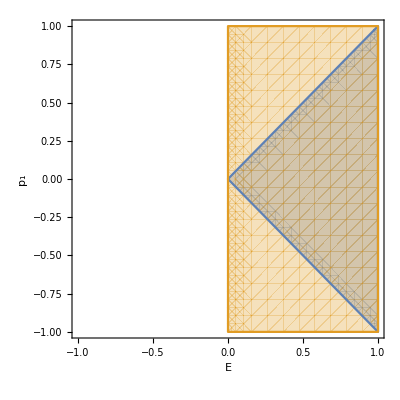

```mathematica
RegionPlot[{reg1,Ee>0},{Ee,-1,1},{pz,-1,1},Axes->True,AxesLabel->{"E",p1}]
```

```mathematica
Exp[-Y]//applyXaXbDefn
```

ⅇ^-Y

```mathematica
kp*km//applyDYkinematics
one=%//applyXaXbDefn

SPD[Vperp[k],Vperp[k]]//applyDYkinematics
two=%//applyXaXbDefn
```

(-ⅇ^NEGY √s √(τ_(+-))+ξ_2 √s-(ℓ_1_⊥)^2/(ξ_1 √s)) (ξ_1 √s-√s √(τ_(+-)) ⅇ^Y-(ℓ_2_⊥)^2/(ξ_2 √s))

(-(√s √(τ_(+-)) x_a)/(√τ)+ξ_1 √s-(ℓ_2_⊥)^2/(ξ_2 √s)) (-(√s √(τ_(+-)) x_b)/(√τ)+ξ_2 √s-(ℓ_1_⊥)^2/(ξ_1 √s))

-2 ℓ_1_⊥·Q_⊥-2 ℓ_2_⊥·Q_⊥-s τ_⊥+2 ℓ_1_⊥·ℓ_2_⊥+(ℓ_1_⊥)^2+(ℓ_2_⊥)^2

-2 ℓ_1_⊥·Q_⊥-2 ℓ_2_⊥·Q_⊥-s τ_⊥+2 ℓ_1_⊥·ℓ_2_⊥+(ℓ_1_⊥)^2+(ℓ_2_⊥)^2

```mathematica
FermionChain[mat]
```

mat

```mathematica
one+two/.Vperp[l1]->0/.Vperp[l2]->0//Expand
FullSimplify[%,Assumptions->0<xa<1&&0<xb<1&&0<xi1<1&&0<xi2<1]
```

(s τ_(+-) x_a x_b)/τ-(ξ_2 s √(τ_(+-)) x_a)/(√τ)-(ξ_1 s √(τ_(+-)) x_b)/(√τ)+ξ_1 ξ_2 s-s τ_⊥

(s (-√(τ_(+-)) √τ (ξ_2 x_a+ξ_1 x_b)+τ_(+-) x_a x_b+ξ_1 ξ_2 τ-τ τ_⊥))/τ

```mathematica
Fier
```

Fier

```mathematica
one//Expand
%/.Vperp[l1]->x/.Vperp[l2]->x

Series[%,{x,0,0}]//Normal
%//FullSimplify
%/.xa*xb->tau//.tau+tauPerp->tauPM//Simplify
%/.tau->xi1*xi2*z
```

(s τ_(+-) x_a x_b)/τ-(ξ_2 s √(τ_(+-)) x_a)/(√τ)+(√(τ_(+-)) x_a (ℓ_1_⊥)^2)/(ξ_1 √τ)-(ξ_1 s √(τ_(+-)) x_b)/(√τ)+(√(τ_(+-)) x_b (ℓ_2_⊥)^2)/(ξ_2 √τ)+ξ_1 ξ_2 s+((ℓ_1_⊥)^2 (ℓ_2_⊥)^2)/(ξ_1 ξ_2 s)-(ℓ_1_⊥)^2-(ℓ_2_⊥)^2

(s τ_(+-) x_a x_b)/τ-(ξ_2 s √(τ_(+-)) x_a)/(√τ)+(√(τ_(+-)) x^2 x_a)/(ξ_1 √τ)-(ξ_1 s √(τ_(+-)) x_b)/(√τ)+(√(τ_(+-)) x^2 x_b)/(ξ_2 √τ)+ξ_1 ξ_2 s+x^4/(ξ_1 ξ_2 s)-2 x^2

(s τ_(+-) x_a x_b)/τ-(ξ_2 s √(τ_(+-)) x_a)/(√τ)-(ξ_1 s √(τ_(+-)) x_b)/(√τ)+ξ_1 ξ_2 s

(s (-√(τ_(+-) τ) (ξ_2 x_a+ξ_1 x_b)+τ_(+-) x_a x_b+ξ_1 ξ_2 τ))/τ

(s (-√(τ_(+-) τ) (ξ_2 x_a+ξ_1 x_b)+ξ_1 ξ_2 τ+τ_(+-) τ))/τ

(s (-√(ξ_1 ξ_2 τ_(+-) z) (ξ_2 x_a+ξ_1 x_b)+ξ_1 ξ_2 τ_(+-) z+ξ_1^2 ξ_2^2 z))/(ξ_1 ξ_2 z)

```mathematica
Integrate[DiracDelta[x1*x2-2(x1+x2)tau*Cosh[Y]+tau],{x1,0,1},Assumptions->1>tau>0&&0<x2<1]
Integrate[%,{x2,0,1},Assumptions->0<tau<1]
```

(x2+τ-2 (x2+1) τ cosh(Y)-τ-2 x2 τ cosh(Y))/(x2-2 τ cosh(Y))

ConditionalExpression[0,cosh(Y)<0]

```mathematica
1-(tau-2*xi2*Sqrt[tauPM]*Cosh[Y])/(xi2-2Sqrt[tauPM]*Cosh[Y])//Together
```

(ξ_2-τ+2 ξ_2 √(τ_(+-)) cosh(Y)-2 √(τ_(+-)) cosh(Y))/(ξ_2-2 √(τ_(+-)) cosh(Y))

```mathematica
ur=(x2 cosh(Y)-τ)/(x2-cosh(Y))
```

(x2 cosh(Y)-τ)/(x2-cosh(Y))

```mathematica
ur
%/.Cosh[Y]->Sqrt[tauPM]Cosh[Y]
%/.Y->0
%/.tauPM->tau//FullSimplify
```

(x2 cosh(Y)-τ)/(x2-cosh(Y))

(√(τ_(+-)) x2 cosh(Y)-τ)/(x2-√(τ_(+-)) cosh(Y))

(√(τ_(+-)) x2-τ)/(x2-√(τ_(+-)))

√τ

#### Model Parton Model 1

```mathematica
fu=4(1-x)
fubar=0

fd=2(1-x)
fdbar=0

fg=0

(* should be 2 *)
Integrate[fu-fubar,{x,0,1}]

(* should be 1 *)
Integrate[fd-fdbar,{x,0,1}]

(* should be 1 *)
Integrate[x(fu+fubar+fd+fdbar+fg),{x,0,1}]
```

4 (1-x)

0

2 (1-x)

0

0

2

1

1

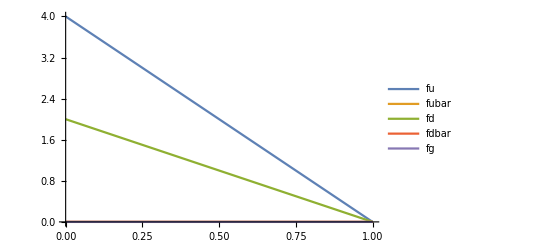

```mathematica
Plot[{fu,fubar,fd,fdbar,fg},{x,0,1},PlotLegends->"Expressions"]
```

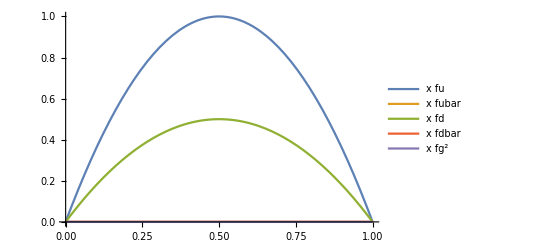

```mathematica
Plot[{x*fu,x*fubar,x*fd,x*fdbar,x*fg^2},{x,0,1},PlotLegends->"Expressions"]
```

#### Model Parton Model 2

```mathematica
fuu=Aa*2(1-x)*Exp[-x]
fuubar=Bb*3(1-x)^2*Exp[-x]

fdd=Ccc*2(1-x)*Exp[-x]
fddbar=Fg*3(1-x)^2*Exp[-x]

fgg=-Gg*Log[x]/x

(* should be 2 *)
Integrate[fuu-fuubar,{x,0,1}]

(* should be 1 *)
Integrate[fdd-fddbar,{x,0,1}]

(* should be 1 *)
Integrate[x(fuu+fuubar+fdd+fddbar+fgg),{x,0,1}]
(Gg/.Solve[%==1])[[1]]
```

2 Aa ⅇ^-x (1-x)

3 Bb ⅇ^-x (1-x)^2

2 Ccc ⅇ^-x (1-x)

3 Fg ⅇ^-x (1-x)^2

-(Gg log(x))/x

(2 (Aa+3 Bb))/ⅇ-3 Bb

(2 Ccc-3 ⅇ Fg+6 Fg)/ⅇ

(-2 (ⅇ-3) Aa+ⅇ (9 Bb-2 Ccc+9 Fg+Gg)+6 (-4 Bb+Ccc-4 Fg))/ⅇ

(2 (ⅇ-3) Aa)/ⅇ-(3 (3 ⅇ-8) Bb)/ⅇ+(2 (ⅇ-3) Ccc)/ⅇ-(3 (3 ⅇ-8) Fg)/ⅇ+1

```mathematica
A=2.8
B=(E/(6-3E))(2-2*A/E)

Cc=1.4
F=(E/(6-3E))(1-2*Cc/E)

G=(1+2*(E-3)*(A+Cc)/E-3*(3*E-8)(B+F)/E)

fu=A*2(1-x)*Exp[-x]
fubar=B*3(1-x)^2*Exp[-x]

fd=Cc*2(1-x)*Exp[-x]
fdbar=F*3(1-x)^2*Exp[-x]

fg=-G*Log[x]/x

(* should be 2 *)
Integrate[fu-fubar,{x,0,1}]

(* should be 1 *)
Integrate[fd-fdbar,{x,0,1}]

(* should be 1 *)
Integrate[x(fu+fubar+fd+fdbar+fg),{x,0,1}]
```

2.8

0.075846

1.4

0.037923

0.109996

5.6 ⅇ^-x (1-x)

0.227538 ⅇ^-x (1-x)^2

2.8 ⅇ^-x (1-x)

0.113769 ⅇ^-x (1-x)^2

-(0.109996 log(x))/x

2.

1.

1.

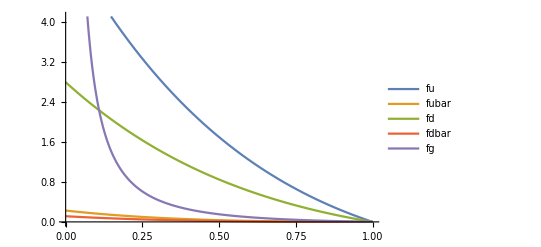

```mathematica
Plot[{fu,fubar,fd,fdbar,fg},{x,0,1},PlotLegends->"Expressions"]
```

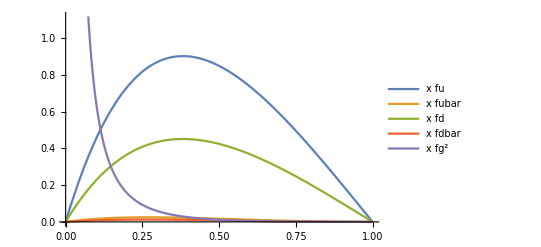

```mathematica
Plot[{x*fu,x*fubar,x*fd,x*fdbar,x*fg^2},{x,0,1},PlotLegends->"Expressions"]
```

#### Model Parton Model 3

```mathematica
fuu=Aa*(2(1-x)^4*Exp[-x]-(1/40)PlusDistribution[HeavisideTheta[x]Log[x]/x])//replSingVarPlus
fuubar=Bb*(1-x)^2/(x+0.01)^2//replSingVarPlus
```

Aa (1/40 (-1/2 log^2(x) x-β-(log(x) x-β)/x)+2 ⅇ^-x (1-x)^4)

(Bb (1-x)^2)/(x+0.01)^2

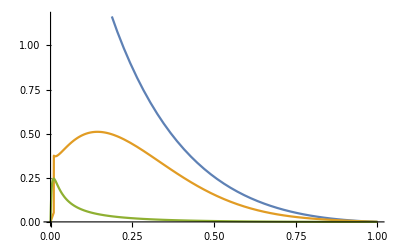

```mathematica
Plot[{x*Log[x/2]^2/x/20+2(1-x)^2Exp[-2x]-Log[2]^2/20,x*fuu/.Aa->A/.beta->0.01,x*fuubar/.Bb->1/100/.beta->0.01},{x,0,1}]
```

```mathematica
width=1/100

fuu=Aa*(2(1-x)^4*Exp[-x]-(1/40)PlusDistribution[HeavisideTheta[x]Log[x]/x])//replSingVarPlus
fuubar=Bb*((1-x)/(x+widtth))^2
fdd=Ccc*(2(1-x)^4*Exp[-x]-(1/15)PlusDistribution[HeavisideTheta[x]Log[x]/x])//replSingVarPlus
fddbar=Ff*((1-x)/(x+widtth))^2

fgg=-Gg*Log[x]/x//replSingVarPlus

(* should be 2 *)
Integrate[fuu-fuubar,{x,0,1},Assumptions->0<beta<1/10&&0<widtth<1/10];
Limit[%,beta->0];
(Bb/.Solve[%==2,Bb])[[1]]
%//StandardForm
(* should be 1 *)
Integrate[fdd-fddbar,{x,0,1},Assumptions->0<beta<1/10&&0<widtth<1/10];
Limit[%,beta->0];
(Ff/.Solve[%==1,Ff])[[1]]
%//StandardForm
(* should be 1 *)
Integrate[x(fuu+fuubar+fdd+fddbar+fgg),{x,0,1},Assumptions->0<beta<1/10&&0<widtth<1/10];
Limit[%,beta->0];
(Gg/.Solve[%==1,Gg])[[1]]
%//StandardForm
```

1/100

Aa (1/40 (-1/2 log^2(x) x-β-(log(x) x-β)/x)+2 ⅇ^-x (1-x)^4)

(Bb (1-x)^2)/(widtth+x)^2

Ccc (1/15 (-1/2 log^2(x) x-β-(log(x) x-β)/x)+2 ⅇ^-x (1-x)^4)

(Ff (1-x)^2)/(widtth+x)^2

-(Gg log(x))/x

$Aborted

Part::partd: Part specification TraditionalForm`Bb ⟦ 1 ⟧ is longer than depth of object.

Bb⟦1⟧

Part::partd: Part specification TraditionalForm`Bb ⟦ 1 ⟧ is longer than depth of object.

Bb⟦1⟧

$Aborted

Part::partd: Part specification TraditionalForm`Ff ⟦ 1 ⟧ is longer than depth of object.

Ff⟦1⟧

Ff⟦1⟧

$Aborted

Part::partd: Part specification TraditionalForm`Gg ⟦ 1 ⟧ is longer than depth of object.

Gg⟦1⟧

Gg⟦1⟧

```mathematica
N@{A,B,Cc,F,G}

WIDTH=0.01;


A=E*1.2/(9E-24)

B=-(2 (-24 A-ⅇ+9 A ⅇ) widtth)/(ⅇ (-1-2 widtth+4 widtth ArcCoth[1+2 widtth]+4 widtth^2 ArcCoth[1+2 widtth]))/.widtth->WIDTH

Cc=E*1.1/(18E-48)
F=((48 Cc+ⅇ-18 Cc ⅇ) widtth)/(ⅇ (-1-2 widtth+4 widtth ArcCoth[1+2 widtth]+4 widtth^2 ArcCoth[1+2 widtth]))/.widtth->WIDTH

G=1/(120 ⅇ)(34560 A+34560 Cc+120 ⅇ-12723 A ⅇ+300 B ⅇ-12728 Cc ⅇ+300 ⅇ F+360 B ⅇ widtth+360 ⅇ F widtth-240 B ⅇ ArcCoth[1+2 widtth]-240 ⅇ F ArcCoth[1+2 widtth]-960 B ⅇ widtth ArcCoth[1+2 widtth]-960 ⅇ F widtth ArcCoth[1+2 widtth]-720 B ⅇ widtth^2 ArcCoth[1+2 widtth]-720 ⅇ F widtth^2 ArcCoth[1+2 widtth])/.widtth->WIDTH

fu=fuu/.Aa->A/.widtth->WIDTH
fubar=fuubar/.Bb->B/.widtth->WIDTH

fd=fdd/.Ccc->Cc/.widtth->WIDTH
fdbar=fddbar/.Ff->F/.widtth->WIDTH

fg=fgg/.Gg->G/.widtth->WIDTH

(* should be 2 *)
Integrate[fu-fubar,{x,0,1},Assumptions->0<beta<1/10];
Limit[%,beta->0]

(* should be 1 *)
Integrate[fd-fdbar,{x,0,1},Assumptions->0<beta<1/10];
Limit[%,beta->0]

(* should be 1 *)
Integrate[x(fu+fubar+fd+fdbar+fg),{x,0,1},Assumptions->0<beta<1/10];
Limit[%,beta->0]
```

{2.8,0.075846,1.4,0.037923,0.109996}

7.02192

0.00431604

3.21838

0.00107901

0.0782428

7.02192 (1/40 (-1/2 log^2(x) x-β-(log(x) x-β)/x)+2 ⅇ^-x (1-x)^4)

(0.00431604 (1-x)^2)/(x+0.01)^2

3.21838 (1/15 (-1/2 log^2(x) x-β-(log(x) x-β)/x)+2 ⅇ^-x (1-x)^4)

(0.00107901 (1-x)^2)/(x+0.01)^2

-(0.0782428 log(x))/x

2.

1.

1.

0.01

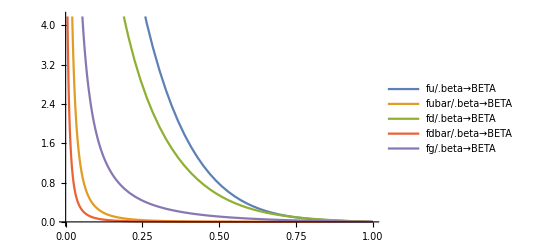

```mathematica
BETA=0.01
Plot[{fu/.beta->BETA,fubar/.beta->BETA,fd/.beta->BETA,fdbar/.beta->BETA,fg/.beta->BETA},{x,0,1},PlotLegends->"Expressions"]
```

0.01

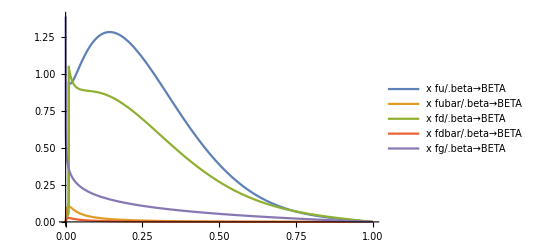

```mathematica
BETA=0.01
Plot[{x*fu/.beta->BETA,x*fubar/.beta->BETA,x*fd/.beta->BETA,x*fdbar/.beta->BETA,x*fg/.beta->BETA},{x,0,1},PlotLegends->"Expressions"]
```

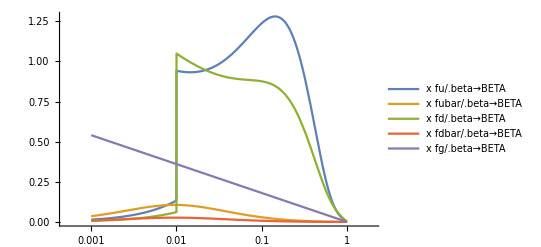

```mathematica
LogLinearPlot[{x*fu/.beta->BETA,x*fubar/.beta->BETA,x*fd/.beta->BETA,x*fdbar/.beta->BETA,x*fg/.beta->BETA},{x,0.001,1},PlotLegends->"Expressions"]
```

#### Model Parton Model 4

```mathematica
fuu=Aa*(2(1-x)^2*Exp[-x]-(1/40)PlusDistribution[HeavisideTheta[x]Log[x]/x])//replSingVarPlus
fuubar=Bb*(1-x)^2/(x+0.01)^2//replSingVarPlus
```

Aa (1/40 (-1/2 log^2(x) x-β-(log(x) x-β)/x)+2 ⅇ^-x (1-x)^2)

(Bb (1-x)^2)/(x+0.01)^2

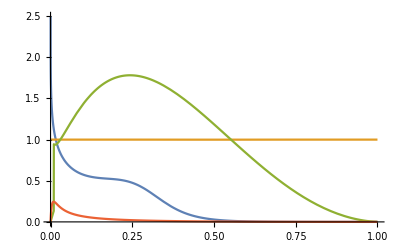

```mathematica
Plot[{-1(Tanh[(x-0.3)10]-1+(1-x)^4Log[x]/x/4)*x,Tanh[1/(x*(1-x))],x*fuu/.Aa->A/.beta->0.01,x*fuubar/.Bb->1/100/.beta->0.01},{x,0,1}]
```

```mathematica
width=1/100

fuu=Aa*(2(1-x)^2*Exp[-x]-(1/40)PlusDistribution[HeavisideTheta[x]Log[x]/x])//replSingVarPlus
fuubar=Bb*((1-x)/(x+widtth))^2
fdd=Ccc*(2(1-x)^2*Exp[-x]-(1/15)PlusDistribution[HeavisideTheta[x]Log[x]/x])//replSingVarPlus
fddbar=Ff*((1-x)/(x+widtth))^2

fgg=-Gg(Tanh[(x-0.3)10]-1+(1-x)^4Log[x]/x/4)//replSingVarPlus

(* should be 2 *)
Integrate[fuu-fuubar,{x,0,1},Assumptions->0<beta<1/10&&0<widtth<1/10];
Limit[%,beta->0];
(Bb/.Solve[%==2,Bb])[[1]]
%//StandardForm
(* should be 1 *)
Integrate[fdd-fddbar,{x,0,1},Assumptions->0<beta<1/10&&0<widtth<1/10];
Limit[%,beta->0];
(Ff/.Solve[%==1,Ff])[[1]]
%//StandardForm
(* should be 1 *)
Integrate[x(fuu+fuubar+fdd+fddbar+fgg),{x,0,1},Assumptions->0<beta<1/10&&0<widtth<1/10];
Limit[%,beta->0];
(Gg/.Solve[%==1,Gg])[[1]]
%//StandardForm
```

1/100

Aa (1/40 (-1/2 log^2(x) x-β-(log(x) x-β)/x)+2 ⅇ^-x (1-x)^2)

(Bb (1-x)^2)/(widtth+x)^2

Ccc (1/15 (-1/2 log^2(x) x-β-(log(x) x-β)/x)+2 ⅇ^-x (1-x)^2)

(Ff (1-x)^2)/(widtth+x)^2

-Gg (((1-x)^4 log(x))/(4 x)+tanh(10 (x-0.3))-1)

-(2 (ⅇ Aa-2 Aa-ⅇ) widtth)/(ⅇ (4 widtth^2 coth^-1(2 widtth+1)-2 widtth+4 widtth coth^-1(2 widtth+1)-1))

-(2 (-2 Aa-ⅇ+Aa ⅇ) widtth)/(ⅇ (-1-2 widtth+4 widtth ArcCoth[1+2 widtth]+4 widtth^2 ArcCoth[1+2 widtth]))

((-2 ⅇ Ccc+4 Ccc+ⅇ) widtth)/(ⅇ (4 widtth^2 coth^-1(2 widtth+1)-2 widtth+4 widtth coth^-1(2 widtth+1)-1))

((4 Ccc+ⅇ-2 Ccc ⅇ) widtth)/(ⅇ (-1-2 widtth+4 widtth ArcCoth[1+2 widtth]+4 widtth^2 ArcCoth[1+2 widtth]))

1/((0.212379 widtth)/(widtth+1.)+0.212379/(widtth+1.))(-(1. Bb widtth log(1.+1/widtth))/(widtth+1.)-(1. Bb log(1.+1/widtth))/(widtth+1.)-(1. Ff widtth log(1.+1/widtth))/(widtth+1.)-(1. Ff log(1.+1/widtth))/(widtth+1.)-(0.138929 Aa widtth)/(widtth+1.)-(0.138929 Aa)/(widtth+1.)-(6. Bb widtth^3 coth^-1(2. widtth+1.))/(widtth+1.)+(3. Bb widtth^2)/(widtth+1.)-(14. Bb widtth^2 coth^-1(2. widtth+1.))/(widtth+1.)+(5.5 Bb widtth)/(widtth+1.)+(2.5 Bb)/(widtth+1.)-(8. Bb widtth coth^-1(2. widtth+1.))/(widtth+1.)-(0.180596 Ccc widtth)/(widtth+1.)-(0.180596 Ccc)/(widtth+1.)-(6. Ff widtth^3 coth^-1(2. widtth+1.))/(widtth+1.)+(3. Ff widtth^2)/(widtth+1.)-(14. Ff widtth^2 coth^-1(2. widtth+1.))/(widtth+1.)+(5.5 Ff widtth)/(widtth+1.)+(2.5 Ff)/(widtth+1.)-(8. Ff widtth coth^-1(2. widtth+1.))/(widtth+1.)+1.)

1/(0.212379/(1.+widtth)+(0.212379 widtth)/(1.+widtth))(1.-(0.138929 Aa)/(1.+widtth)+(2.5 Bb)/(1.+widtth)-(0.180596 Ccc)/(1.+widtth)+(2.5 Ff)/(1.+widtth)-(0.138929 Aa widtth)/(1.+widtth)+(5.5 Bb widtth)/(1.+widtth)-(0.180596 Ccc widtth)/(1.+widtth)+(5.5 Ff widtth)/(1.+widtth)+(3. Bb widtth^2)/(1.+widtth)+(3. Ff widtth^2)/(1.+widtth)-(8. Bb widtth ArcCoth[1.+2. widtth])/(1.+widtth)-(8. Ff widtth ArcCoth[1.+2. widtth])/(1.+widtth)-(14. Bb widtth^2 ArcCoth[1.+2. widtth])/(1.+widtth)-(14. Ff widtth^2 ArcCoth[1.+2. widtth])/(1.+widtth)-(6. Bb widtth^3 ArcCoth[1.+2. widtth])/(1.+widtth)-(6. Ff widtth^3 ArcCoth[1.+2. widtth])/(1.+widtth)-(1. Bb Log[1.+1/widtth])/(1.+widtth)-(1. Ff Log[1.+1/widtth])/(1.+widtth)-(1. Bb widtth Log[1.+1/widtth])/(1.+widtth)-(1. Ff widtth Log[1.+1/widtth])/(1.+widtth))

```mathematica
N@{A,B,Cc,F,G}

WIDTH=0.01;


A=E*1.001/(E-2)

B=-(2 (-2 Aa-ⅇ+Aa ⅇ) widtth)/(ⅇ (-1-2 widtth+4 widtth ArcCoth[1+2 widtth]+4 widtth^2 ArcCoth[1+2 widtth]))/.widtth->WIDTH/.Aa->A/.Bb->B/.Ccc->Cc/.Ff->F

Cc=E*1.001/(2E-4)
F=((4 Ccc+ⅇ-2 Ccc ⅇ) widtth)/(ⅇ (-1-2 widtth+4 widtth ArcCoth[1+2 widtth]+4 widtth^2 ArcCoth[1+2 widtth]))/.widtth->WIDTH/.Aa->A/.Bb->B/.Ccc->Cc/.Ff->F

G=1/(0.21237886360136043/(1.+widtth)+(0.21237886360136043 widtth)/(1.+widtth))(1.-(0.1389289412569227 Aa)/(1.+widtth)+(2.5 Bb)/(1.+widtth)-(0.18059560792358867 Ccc)/(1.+widtth)+(2.5 Ff)/(1.+widtth)-(0.1389289412569227 Aa widtth)/(1.+widtth)+(5.5 Bb widtth)/(1.+widtth)-(0.18059560792358867 Ccc widtth)/(1.+widtth)+(5.5 Ff widtth)/(1.+widtth)+(3. Bb widtth^2)/(1.+widtth)+(3. Ff widtth^2)/(1.+widtth)-(7.999999999999999 Bb widtth ArcCoth[1.+2. widtth])/(1.+widtth)-(7.999999999999999 Ff widtth ArcCoth[1.+2. widtth])/(1.+widtth)-(14. Bb widtth^2 ArcCoth[1.+2. widtth])/(1.+widtth)-(14. Ff widtth^2 ArcCoth[1.+2. widtth])/(1.+widtth)-(6. Bb widtth^3 ArcCoth[1.+2. widtth])/(1.+widtth)-(6. Ff widtth^3 ArcCoth[1.+2. widtth])/(1.+widtth)-(0.9999999999999999 Bb Log[1.+1/widtth])/(1.+widtth)-(0.9999999999999999 Ff Log[1.+1/widtth])/(1.+widtth)-(0.9999999999999999 Bb widtth Log[1.+1/widtth])/(1.+widtth)-(0.9999999999999999 Ff widtth Log[1.+1/widtth])/(1.+widtth))/.widtth->WIDTH/.Aa->A/.Bb->B/.Ccc->Cc/.Ff->F

fu=fuu/.Aa->A/.widtth->WIDTH
fubar=fuubar/.Bb->B/.widtth->WIDTH

fd=fdd/.Ccc->Cc/.widtth->WIDTH
fdbar=fddbar/.Ff->F/.widtth->WIDTH

fg=fgg/.Gg->G/.widtth->WIDTH

(* should be 2 *)
Integrate[fu-fubar,{x,0,1},Assumptions->0<beta<1/10];
Limit[%,beta->0]

(* should be 1 *)
Integrate[fd-fdbar,{x,0,1},Assumptions->0<beta<1/10];
Limit[%,beta->0]

(* should be 1 *)
Integrate[x(fu+fubar+fd+fdbar+fg),{x,0,1},Assumptions->0<beta<1/10];
Limit[%,beta->0]
```

{7.02192,0.00431604,3.21838,0.00107901,0.0782428}

3.78821

0.0000215802

1.8941

0.0000107901

0.619497

3.78821 (1/40 (-1/2 log^2(x) x-β-(log(x) x-β)/x)+2 ⅇ^-x (1-x)^2)

(0.0000215802 (1-x)^2)/(x+0.01)^2

1.8941 (1/15 (-1/2 log^2(x) x-β-(log(x) x-β)/x)+2 ⅇ^-x (1-x)^2)

(0.0000107901 (1-x)^2)/(x+0.01)^2

-0.619497 (((1-x)^4 log(x))/(4 x)+tanh(10 (x-0.3))-1)

2.

1.

1.

0.01

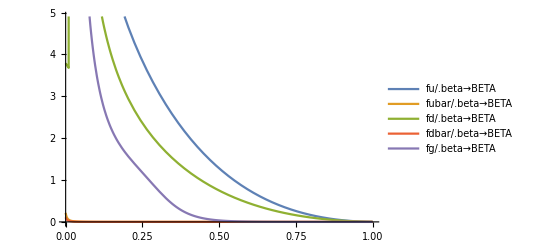

```mathematica
BETA=0.01
Plot[{fu/.beta->BETA,fubar/.beta->BETA,fd/.beta->BETA,fdbar/.beta->BETA,fg/.beta->BETA},{x,0,1},PlotLegends->"Expressions"]
```

0.01

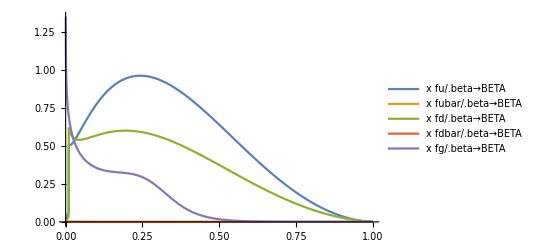

```mathematica
BETA=0.01
Plot[{x*fu/.beta->BETA,x*fubar/.beta->BETA,x*fd/.beta->BETA,x*fdbar/.beta->BETA,x*fg/.beta->BETA},{x,0,1},PlotLegends->"Expressions"]
```

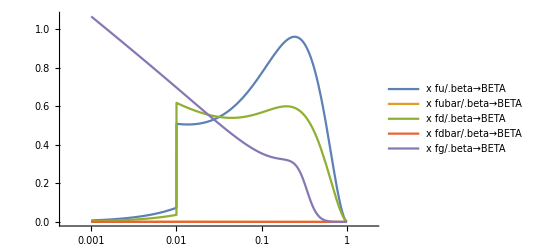

```mathematica
LogLinearPlot[{x*fu/.beta->BETA,x*fubar/.beta->BETA,x*fd/.beta->BETA,x*fdbar/.beta->BETA,x*fg/.beta->BETA},{x,0.001,1},PlotLegends->"Expressions"]
```